## The Plant Functions

## Observations

```mathematica
(* 0 - Prioridade: Verificar a função ivpPlant1, partes que envolvem mudanças de variáveis. *)
(* Precisa testar ivpPlant1.*)
(* 1 - UTILIZAR A FUNÇÃO ivpPlant1, COM FOCO NAS VARIÁVEIS COMMANDS, EQS0 E STEPS *)
(* 2 - AS VARIÁVEIS COMMANDS E STEPS PODEM VARIAR E ESTÃO RELACIONADAS AOS INPUTS DOS ATUADORES E A AMOSTRAGEM, *)(* RESPECTIVAMENTE *)
(* 3 - A VARIÁVEL EQS0 ESTÁ RELACIONADA COM O ÚLTIMO ESTADO DA PLANTA, SERVINDO ASSIM COMO CONDIÇÃO(ÕES) *) (* INICIAL(IS) DA AMOSTRA SEGUINTE *)
(* 4 - É NECESSÁRIO IMPLEMENTAR A MODELAGEM EM ESPAÇO DE ESTADOS PARA ANÁLISE DA OBSERVABILIDADE/CONTROLABILIDADE *)
(* 5 - Incorporar a algebra de quatérnios, trazendo as representações vetoriais para o CM *)
(* ν , α , p , ζ correspondem respectivamente aos vetores velocidade linear, velocidade angular, posição e atitude *)
```

## Base functions

### The basic structures

Id[n_] := IdentityMatrix[n]

pot[matriz_, n_] := MatrixPower[matriz, n]

```mathematica
crossvector[vectorA_,vectorB_]:={{0,-vectorA[[3]],vectorA[[2]]},{vectorA[[3]],0,-vectorA[[1]]},{-vectorA[[2]],vectorA[[1]],0}}.vectorB
til[vector_]:={{0,-vector[[3]],vector[[2]]},{vector[[3]],0,-vector[[1]]},{-vector[[2]],vector[[1]],0}}(*Til matrix to a vector - for vectoral product*)
vectorbytil[til_]:={til[[3,2]],til[[1,3]],til[[2,1]]}(*3th line and 2nd column, 1st line and 3th column, 2nd line and 1st column*)
```

### The function of rotation matrix

```mathematica
rotationMatrix[axis_,angle_]:=Block[{rotationaxis=axis,axiscomparative,deltaangle=angle,x,y,z,fnew,test},
(* Kernel Function of solution *)
test[rotationaxis_,axiscomparative_]:=rotationaxis==axiscomparative;
(* Look of solution *)
Do[
If[test[rotationaxis,x],fnew={{1,0,0},{0,Cos[deltaangle],Sin[deltaangle]},{0,-Sin[deltaangle],Cos[deltaangle]}}];
If[test[rotationaxis,y],fnew={{Cos[deltaangle],0,-Sin[deltaangle]},{0,1,0},{Sin[deltaangle],0,Cos[deltaangle]}}];If[test[rotationaxis,z],fnew={{Cos[deltaangle],Sin[deltaangle],0},{-Sin[deltaangle],Cos[deltaangle],0},{0,0,1}}],
1];
Return[fnew] (*to see all grid points*)]
```

```mathematica
rotationMatrix[x,ϕ]//MatrixForm
rotationMatrix[y,θ]//MatrixForm
rotationMatrix[z,ψ]//MatrixForm
```

(1 | 0 | 0
0 | Cos[ϕ] | Sin[ϕ]
0 | -Sin[ϕ] | Cos[ϕ])

(Cos[θ] | 0 | -Sin[θ]
0 | 1 | 0
Sin[θ] | 0 | Cos[θ])

(Cos[ψ] | Sin[ψ] | 0
-Sin[ψ] | Cos[ψ] | 0
0 | 0 | 1)

### The function of quaternion and your properties

#### a) Quaternion Function - quatNot( (portion1, portion2, portion3, portion4), (QN, CJG, EUCNORM, INV, VP, SP, PM, Cayley, ALL) ) QN - quaternion notation; CJG - quaternion conjugate; EUCNORM - Euclidean Norm; INV - inverse quaternion; VP - vector part; SP - scalar part; PM - product matrix; Cayley - Cayley matrix; and ALL - All elements.

```mathematica
quatNot[{portion1_,portion2_,portion3_,portion4_},option_]:=Block[{quaternion,quaterniontilmatrix,quaternionconjungate,quaternionnorm,quaternioninverse,vectorportionbyquaternion,scalarportion,CayleyMatrix,test,fnew,til,QN,CJG,EUCNORM,INV, VP, SP, PM,Cayley,ALL},
(* Kernel Function of solution *)
(*til[vector_]:={{0,-vector[[3]],vector[[2]]},{vector[[3]],0,-vector[[1]]},{-vector[[2]],vector[[1]],0}};*)
quaternion={portion1,portion2,portion3,portion4};
vectorportionbyquaternion=quaternion[[1;;3]];
scalarportion=quaternion[[4]];
quaternionconjungate=Flatten[{-vectorportionbyquaternion,scalarportion}];
 quaternioninverse=(1/(Norm[quaternion,2])^2) quaternionconjungate;
 quaternionnorm=Norm[quaternion,2];quaterniontilmatrix=Transpose[Append[Transpose[Append[scalarportion IdentityMatrix[3]+{{0,-vectorportionbyquaternion[[3]],vectorportionbyquaternion[[2]]},{vectorportionbyquaternion[[3]],0,-vectorportionbyquaternion[[1]]},{-vectorportionbyquaternion[[2]],vectorportionbyquaternion[[1]],0}},-vectorportionbyquaternion]],Flatten[{vectorportionbyquaternion,scalarportion}]]];
CayleyMatrix={{(portion1^2-portion2^2-portion3^2+portion4^2),2(portion1 portion2-portion3 portion4),2(portion1 portion3+portion2 portion4)},{2(portion1 portion2+portion3 portion4),(portion2^2-portion1^2+portion4^2-portion3^2),2(portion3 portion2-portion1 portion4)},{2(portion1 portion3-portion2 portion4),2(portion1 portion4+portion2 portion3),(portion3^2-portion1^2+portion4^2-portion2^2)}};
test[fnc_,cmd_]:=fnc==cmd;
(* Loop of solution *)
Do[
If[test[option,QN],fnew=quaternion];
If[test[option,CJG],fnew=quaternionconjungate];
If[test[option,EUCNORM],fnew=quaternionnorm];
If[test[option,INV],fnew=quaternioninverse];
If[test[option,VP],fnew=vectorportionbyquaternion];
If[test[option,SP],fnew=scalarportion];
If[test[option,PM],fnew=quaterniontilmatrix];
If[test[option,Cayley],fnew=CayleyMatrix];
If[test[option,ALL],fnew={quaternion,quaternionconjungate,quaternionnorm,quaternioninverse,vectorportionbyquaternion,scalarportion,quaterniontilmatrix,CayleyMatrix}];
,1];
Return[fnew] (*to see all grid points*)]
```

#### b) Unit quaternion ||n|| = 1 --- unitQuati(axis, angle)

```mathematica
unitQuati[axis_,angle_]:=
Block[{unitquaternion,test,univectori, univectorj,univectork, fnew,x,y,z},
(* Kernel Function of solution *)
test[fnc_,cmd_]:=fnc==cmd;
(* Loop of solution *)
univectori={1,0,0};
univectorj={0,1,0};
univectork={0,0,1};
Do[
If[test[axis,x],fnew=Flatten[{-univectori  Sin[angle/2],Cos[angle/2]}]];
If[test[axis,y],fnew=Flatten[{-univectorj  Sin[angle/2],Cos[angle/2]}]];
If[test[axis,z],fnew=Flatten[{-univectork  Sin[angle/2],Cos[angle/2]}]];
,1];
Return[fnew] (*to see all grid points*)]
```

#### c) Product Matrix or quatNot Function - PMorQuatNot( entity, (QN - quanternion notation, PM - product matrix) )

```mathematica
PMorQuatNot[entity_]:=Block[{QN, PM, test, dimension, length, fnew},
(* Kernel Function of solution *)
dimension=Dimensions[entity];
length=Length[dimension];
test[fnc_,cmd_]:=fnc==cmd;
(* Loop of solution *)
Do[
(*If[test[option,QN],fnew=quaternion];
If[test[option,MP],fnew=quaterniontilmatrix];*)
If[length==1,fnew=quatNot[entity,PM]];
If[length==2,fnew=Transpose[entity][[4]]];
,1];
Return[fnew] (*to see all grid points*)]
```

#### d) QuatDeriv( If entity is a pure vector quaternion, DerivativeOption is 1. Otherwise, it is 2.) (under evaluation)

```mathematica
QuatDeriv[entity_,DerivativeOption_(*If entity is a pure vector quaternion, DerivativeOption is 1.  Otherwise, it is 2.*)]:=Block[{test1,test2,fnew},
(* Kernel Function of solution *)
test1[fnc_,cmd_]:=fnc==cmd;
(* Loop of solution *)
Do[
If[DerivativeOption==1,fnew=(1/2) Evaluate[quatNot[{q1,q2,q3,q4},PM].entity]];
If[DerivativeOption==2,fnew=-(1/2) Evaluate[quatNot[entity,PM].{q1,q2,q3,q4}]]
,1];
(*fnew=-(1/2) quatNot[{q1,q2,q3,q4},PM].entity,1];*)
Return[fnew] (*to see all grid points*)]
```

#### e) Attitude Representation by Quaternions ( If entity is a pure vector quaternion, DerivativeOption is 1. Otherwise, it is 2.) (in progressing)

QuatDeriv2[entity_, DerivativeOption_(*If entity is a pure vector quaternion, DerivativeOption is 1.  Otherwise, it is 2.*)] := Block[{test1, test2, fnew},
  (* Kernel Function of solution *)
  test1[fnc_, cmd_] := fnc == cmd;
  (* Loop of solution *)
  Do[
   If[DerivativeOption == 1, fnew = (1/2) Evaluate[quatNot[{q1, q2, q3, q4}, PM] . entity]];
   If[DerivativeOption == 2, fnew = -(1/2) Evaluate[quatNot[entity, PM] . {q1, q2, q3, q4}]]
   , 1];
  (*fnew=-(1/2) quatNot[{q1,q2,q3,q4},PM].entity,1];*)
  Return[fnew] (*to see all grid points*)]

### The conversion function of Quaternion to Euler Angles (in implementation)

#### a) Quaternion Function - QuatToEulerToQuat( (portion1, portion2, portion3, portion4), (Qrepres, CJG, VP, SP, MP, Cayley, ALL) )

QuatToEulerToQuat[entity_, option_] := Block[{quaternion, quaterniontilmatrix, quaternionconjungate, vectorportionbyquaternion, scalarportion, CayleyMatrix, test, fnew, til, Qrepres, CJG, VP, SP, MP, Cayley, ALL},
  (* Kernel Function of solution *)
  (*til[vector_]:={{0,-vector[[3]],vector[[2]]},{vector[[3]],0,-vector[[1]]},{-vector[[2]],vector[[1]],0}};*)
  quaternion = entity;
  vectorportionbyquaternion = quaternion[[1 ;; 3]];
  scalarportion = quaternion[[4]];
  quaternionconjungate = Flatten[{-vectorportionbyquaternion, scalarportion}]; quaterniontilmatrix = Transpose[Append[Transpose[Append[scalarportion IdentityMatrix[3] + {{0, -vectorportionbyquaternion[[3]], vectorportionbyquaternion[[2]]}, {vectorportionbyquaternion[[3]], 0, -vectorportionbyquaternion[[1]]}, {-vectorportionbyquaternion[[2]], vectorportionbyquaternion[[1]], 0}}, -vectorportionbyquaternion]], Flatten[{vectorportionbyquaternion, scalarportion}]]];
  test[fnc_, cmd_] := fnc == cmd;
  (* Loop of solution *)
  Do[
   If[test[option, Qrepres], fnew = quaternion];
   If[test[option, CJG], fnew = quaternionconjungate];
   If[test[option, VP], fnew = vectorportionbyquaternion];
   If[test[option, SP], fnew = scalarportion];
   If[test[option, MP], fnew = quaterniontilmatrix];
   If[test[option, Cayley], fnew = CayleyMatrix];
   If[test[option, ALL], fnew = {quaternion, quaternionconjungate, vectorportionbyquaternion, scalarportion, quaterniontilmatrix, CayleyMatrix}];
   , 1];
  Return[fnew] (*to see all grid points*)]

### Orientation Matrix by:

#### a) Successive Rotations - Euler Notation - Euler(α, β, γ)

{x,y,z}⟹ {x’, y’, z} ⟹ {x’, y’’, z’’}⟹{x’’’,y’’’,z’’}
    F                P(α)                  Q(β)                   R(γ)

```mathematica
Euler[α_,β_,γ_]:=rotationMatrix[z,α].rotationMatrix[x,β].rotationMatrix[z,γ]
```

#### b) Successive Rotations - Tait-Bryan Notation - TaitBryan(α, β, γ)

{x,y,z}⟹ {x,y’,z’} ⟹ {x’’,y’,z’’}⟹{x’’’,y’’’,z’’}
    F               P(α)                 Q(β)                R(γ)

```mathematica
TaitBryan[α_,β_,γ_]:=rotationMatrix[x,α].rotationMatrix[y,β].rotationMatrix[z,γ]
```

```mathematica
rotationMatrix[z,α]
```

{{Cos[α],Sin[α],0},{-Sin[α],Cos[α],0},{0,0,1}}

#### c) Single Rotation - Euler Vector and Transformation Matrix - EVectorOrTMatrix (element, EV = Euler or TM = Transformation Matrix)

```mathematica
EVectorOrTMatrix[entity_,option_(*EV = Euler or TM = Transformation Matrix*)]:=Block[{test,fnew, Tanti, Tsimet,twister,twisterVersor, theta,sintheta,costheta, twisterTil, EV, TM},
(* Kernel Function of solution *)
test[fnc_,cmd_]:=fnc==cmd;
(* Loop of solution *)
Do[
If[test[option,EV],
Tanti=1/2 (entity-Transpose[entity]);
Tsimet=1/2 (entity+Transpose[entity]);
twister={Tanti[[3,2]],Tanti[[1,3]],Tanti[[2,1]]};
twisterVersor=twister/Norm[twister];
sintheta=Norm[twister];
theta=ArcSin[sintheta];
fnew={twisterVersor,twister,theta}];
If[test[option,TM],
twister=entity[[1;;3]];
theta=entity[[4]];
sintheta=Sin[theta];
costheta=Cos[theta];
twisterTil={{0,-Evaluate[twister/Norm[twister]][[3]],Evaluate[twister/Norm[twister]][[2]]},{Evaluate[twister/Norm[twister]][[3]],0,-Evaluate[twister/Norm[twister]][[1]]},{-Evaluate[twister/Norm[twister]][[2]],Evaluate[twister/Norm[twister]][[1]],0}};
fnew=IdentityMatrix[3]+sintheta twisterTil+((1-Cos[theta]) MatrixPower[twisterTil,2])]
,1];
Return[fnew] (*to see all grid points*)]
```

#### d) Transformation Matrix by Points of Space - MatrixByThreePoints(initialpoints, finalpoints, S = simple or M = MatrixForm)

```mathematica
TMatrixByThreePoints[initialpoints_,finalpoints_,option_(*S = simple or M = MatrixForm*)]:=Block[{Ipoints=initialpoints , Fpoints=finalpoints , consist, Titofby3pts,S,M},
(* Kernel Function of solution *)
(* Loop of solution *)
Do[(* Consistency tests and Processing *)
If[N[Norm[Ipoints[[1]]-Ipoints[[2]]]]==N[Norm[Fpoints[[1]]-Fpoints[[2]]]],consist="Consistence is ok!";If[option==S,Titofby3pts=Transpose[Ipoints].Inverse[Transpose[Fpoints]]];If[option==M,Titofby3pts=MatrixForm[Transpose[Ipoints].Inverse[Transpose[Fpoints]]]],consist="Consistence isn't ok!"],1];
Return[Titofby3pts] (*to see all grid points*)]
```

#### e) Transformation Matrix by Two Vector in different SR - TMatrixByTwoVectors(initialvector, finalvector, S = simple or M = MatrixForm)

```mathematica
TMatrixByTwoVectors[initialvector_,finalvector_,option_(*S = simple or M = MatrixForm*)]:=Block[{Ipoints=initialvector , Fpoints=finalvector , consist, Titofby2v,S,M},
(* Kernel Function of solution *)

(* Loop of solution *)
Do[(* Consistency tests and Processing *)
If[N[Norm[Ipoints[[1]]-Ipoints[[2]]]]==N[Norm[Fpoints[[1]]-Fpoints[[2]]]],consist="Consistence is ok!";If[option==S,Titofby2v=Transpose[Ipoints].Inverse[Transpose[Fpoints]]];If[option==M,Titofby2v=MatrixForm[Transpose[Ipoints].Inverse[Transpose[Fpoints]]]],consist="Consistence isn't ok!"],1];
Return[Titofby2v] (*to see all grid points*)]
```

#### f) Transformation Matrix to Quaternion - TMorQuaternion(entity, TM = Transformation Matrix or QN = Quaternion Notation)

```mathematica
TMorQuaternion[entity_,option_]:=Block[{test,fnew, Tanti, Tsimet,twister,twisterVersor, theta,sintheta,costheta,TM, QN,qvector,scalarportionsqrd,scalarportion,vectorpart,portion1,portion2,portion3,portion4,sol,Transmatrix},
test[fnc_,cmd_]:=fnc==cmd;
(* Kernel Function of solution *)
(* quatNot[{portion1_,portion2_,portion3_,portion4_},option_]  *)
(* Loop of solution *)
(*Id[n],pot[matriz,n]*)
Do[If[test[option,QN],
Tanti=1/2 (entity-Transpose[entity]);
Tsimet=1/2 (entity+Transpose[entity]);
scalarportionsqrd=((1/2) (MatrixPower[Tanti,2])/(Tsimet-IdentityMatrix[Length[Tsimet]]));
scalarportion=scalarportionsqrd^(1/2);
scalarportion=scalarportion[[1]][[1]];(*Only a term is suficient!*)
qvector=vectorbytil[Tanti];
fnew=Flatten[{qvector,scalarportion}]];
If[test[option,TM],
vectorpart=entity[[1;;3]];
scalarportion=entity[[4]];
twister = Evaluate[vectorpart/Norm[vectorpart]];
theta=ArcCos[2 (scalarportion^2)-1];
sol=Flatten[{twister,theta}];
Transmatrix=EVectorOrTMatrix[sol,TM];
fnew={sol,Transmatrix}];
,1];
Return[fnew] (*to see all grid points*)]
```

### Examples:

#### a. Transforming the Coordinates with Cardanical Angles

```mathematica
Tϕθψ=rotationMatrix[z,ψ].rotationMatrix[y,θ].rotationMatrix[x,ϕ];
Tϕθψ//MatrixForm
```

(Cos[θ] Cos[ψ] | Cos[ψ] Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[ψ] | -Cos[ϕ] Cos[ψ] Sin[θ]+Sin[ϕ] Sin[ψ]
-Cos[θ] Sin[ψ] | Cos[ϕ] Cos[ψ]-Sin[θ] Sin[ϕ] Sin[ψ] | Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[θ] Sin[ψ]
Sin[θ] | -Cos[θ] Sin[ϕ] | Cos[θ] Cos[ϕ])

```mathematica
p̲={ϕ̇,0,0};
q̲={0,θ̇,0};
r̲={0,0,ψ̇};
```

```mathematica
(* Mapeando de ξ para ζ *)
```

```mathematica
TΩ=p̲+(rotationMatrix[x,ϕ].q̲)+(rotationMatrix[x,ϕ].rotationMatrix[y,θ].r̲);
TΩ//MatrixForm
```

(ϕ̇-ψ̇ Sin[θ]
Cos[ϕ] θ̇+Cos[θ] ψ̇ Sin[ϕ]
Cos[θ] Cos[ϕ] ψ̇-θ̇ Sin[ϕ])

```mathematica
TΩ={{1,0,-Sin[θ]},{0,Cos[ϕ],Cos[θ] Sin[ϕ]},{0,-Sin[ϕ],Cos[θ] Cos[ϕ]}};
TΩ//MatrixForm
```

(1 | 0 | -Sin[θ]
0 | Cos[ϕ] | Cos[θ] Sin[ϕ]
0 | -Sin[ϕ] | Cos[θ] Cos[ϕ])

```mathematica
Inverse[TΩ]//Simplify//MatrixForm
```

(1 | Sin[ϕ] Tan[θ] | Cos[ϕ] Tan[θ]
0 | Cos[ϕ] | -Sin[ϕ]
0 | Sec[θ] Sin[ϕ] | Cos[ϕ] Sec[θ])

#### b. Transforming the Coordinates

O mínimo alcance dos ângulos de Euler para cobrir toda a extensão de rotações pode ser definido pelos intervalos [-π, π), [-π/2, π/2] e [0, 2π) para θx, θy e θz, respectivamente, podendo variar convenientemente para diferentes aplicações. No entanto, nota-se que este grupo não é topologicamente equivalente a SO(3), pois existem certos casos nos quais uma única rotação possui um número infinito de soluções. Por exemplo, do ponto de vista dos eixos do corpo, para um ângulo de arfagem (θ) igual a +/-π/2, os eixos de rolamento e guinada ficam alinhados, logo, quando a aeronave aponta seu nariz para cima os ângulos ϕ e ψ são equivalentes, i.e., para δ pertencente aos Reais.

{ψ, π/2, ϕ} coincidente {ψ - δ, π/2,  ϕ - δ }
{ψ, - π/2, ϕ} coincidente {ψ - δ,- π/2,  ϕ + δ }

Estas condições são singularidades matemáticas, denotadas por gimbal lock_14.

```mathematica
cmatrix={{c11,c12,c13}{c21,c22,c23}{c31,c32,c33}};
```

```mathematica
quatNot[{q1,q2,q3,q4},Cayley]//MatrixForm
```

(q1^2-q2^2-q3^2+q4^2 | 2 (q1 q2-q3 q4) | 2 (q1 q3+q2 q4)
2 (q1 q2+q3 q4) | -q1^2+q2^2-q3^2+q4^2 | 2 (q2 q3-q1 q4)
2 (q1 q3-q2 q4) | 2 (q2 q3+q1 q4) | -q1^2-q2^2+q3^2+q4^2)

```mathematica
QΩ=quatNot[unitQuater[x,ϕ],PM].quatNot[unitQuater[y,θ],PM].unitQuater[z,ψ];QΩ//MatrixForm
quatNot[QΩ,Cayley].{ω1,ω2,ω3}//MatrixForm//FullSimplify
```

quatNot[unitQuater[x,ϕ],PM].quatNot[unitQuater[y,θ],PM].unitQuater[z,ψ]

quatNot[quatNot[unitQuater[x,ϕ],PM].quatNot[unitQuater[y,θ],PM].unitQuater[z,ψ],Cayley].{ω1,ω2,ω3}

```mathematica
unitQuati[y,ω]
```

{0,-Sin[ω/2],0,Cos[ω/2]}

```mathematica
univectorx={1,0,0};
univectory={0,1,0};
univectorz={0,0,1};
```

```mathematica
Subscript[Q, iofϕ]=unitQuati[x,ϕ/2];
Subscript[Q, jofθ]=unitQuati[y,θ/2];
Subscript[Q, kofψ]=unitQuati[z,ψ/2];
Tϕθψquat=quatNot[Subscript[Q, iofϕ],Cayley].quatNot[Subscript[Q, jofθ],Cayley].quatNot[Subscript[Q, kofψ],Cayley]//MatrixForm//FullSimplify
Tϕθψquat=quatNot[quatNot[Subscript[Q, iofϕ],PM].quatNot[Subscript[Q, jofθ],PM].Subscript[Q, kofψ],Cayley]//MatrixForm//FullSimplify
```

(Cos[θ/2] Cos[ψ/2] | Cos[θ/2] Sin[ψ/2] | -Sin[θ/2]
Cos[ψ/2] Sin[θ/2] Sin[ϕ/2]-Cos[ϕ/2] Sin[ψ/2] | Cos[ϕ/2] Cos[ψ/2]+Sin[θ/2] Sin[ϕ/2] Sin[ψ/2] | Cos[θ/2] Sin[ϕ/2]
Cos[ϕ/2] Cos[ψ/2] Sin[θ/2]+Sin[ϕ/2] Sin[ψ/2] | -Cos[ψ/2] Sin[ϕ/2]+Cos[ϕ/2] Sin[θ/2] Sin[ψ/2] | Cos[θ/2] Cos[ϕ/2])

(Cos[θ/2] Cos[ψ/2] | Cos[θ/2] Sin[ψ/2] | -Sin[θ/2]
Cos[ψ/2] Sin[θ/2] Sin[ϕ/2]-Cos[ϕ/2] Sin[ψ/2] | Cos[ϕ/2] Cos[ψ/2]+Sin[θ/2] Sin[ϕ/2] Sin[ψ/2] | Cos[θ/2] Sin[ϕ/2]
Cos[ϕ/2] Cos[ψ/2] Sin[θ/2]+Sin[ϕ/2] Sin[ψ/2] | -Cos[ψ/2] Sin[ϕ/2]+Cos[ϕ/2] Sin[θ/2] Sin[ψ/2] | Cos[θ/2] Cos[ϕ/2])

```mathematica
quatNot[Subscript[Q, iofϕ],MP].quatNot[Subscript[Q, iofϕ],CJG]//FullSimplify
```

fnew.{Sin[ϕ/4],0,0,Cos[ϕ/4]}

```mathematica
qunivectorx=quatNot[Flatten[{p̲,0}],Qrepres];
qunivectory=quatNot[Flatten[{q̲,0}],Qrepres];
qunivectorz=quatNot[Flatten[{r̲,0}],Qrepres];
```

```mathematica
rotationMatrix[x,ϕ]//MatrixForm
rotationMatrix[y,θ]//MatrixForm
rotationMatrix[z,ψ]//MatrixForm
```

(1 | 0 | 0
0 | Cos[ϕ] | Sin[ϕ]
0 | -Sin[ϕ] | Cos[ϕ])

(Cos[θ] | 0 | -Sin[θ]
0 | 1 | 0
Sin[θ] | 0 | Cos[θ])

(Cos[ψ] | Sin[ψ] | 0
-Sin[ψ] | Cos[ψ] | 0
0 | 0 | 1)

```mathematica
p̲={ϕ̇,0,0};
q̲={0,θ̇,0};
r̲={0,0,ψ̇};
```

```mathematica
(* Mapeando de ξ para ζ *)
```

```mathematica
TΩ=p̲+(rotationMatrix[x,ϕ].q̲)+(rotationMatrix[x,ϕ].rotationMatrix[y,θ].r̲);
TΩ//MatrixForm
```

(ϕ̇-ψ̇ Sin[θ]
Cos[ϕ] θ̇+Cos[θ] ψ̇ Sin[ϕ]
Cos[θ] Cos[ϕ] ψ̇-θ̇ Sin[ϕ])

```mathematica
TMorQuaternion[{q1,q2,q3,q4},TM][[2]]//FullSimplify//MatrixForm
```

((2 (q2^2+q3^2) (-1+q4^2)+Abs[q1]^2+Abs[q2]^2+Abs[q3]^2)/(Abs[q1]^2+Abs[q2]^2+Abs[q3]^2) | -(2 (q1 q2 (-1+q4^2)+q3 √(-q4^2 (-1+q4^2) (Abs[q1]^2+Abs[q2]^2+Abs[q3]^2))))/(Abs[q1]^2+Abs[q2]^2+Abs[q3]^2) | (-2 q1 q3 (-1+q4^2)+2 q2 √(-q4^2 (-1+q4^2) (Abs[q1]^2+Abs[q2]^2+Abs[q3]^2)))/(Abs[q1]^2+Abs[q2]^2+Abs[q3]^2)
(-2 q1 q2 (-1+q4^2)+2 q3 √(-q4^2 (-1+q4^2) (Abs[q1]^2+Abs[q2]^2+Abs[q3]^2)))/(Abs[q1]^2+Abs[q2]^2+Abs[q3]^2) | (2 (q1^2+q3^2) (-1+q4^2)+Abs[q1]^2+Abs[q2]^2+Abs[q3]^2)/(Abs[q1]^2+Abs[q2]^2+Abs[q3]^2) | -(2 (q2 q3 (-1+q4^2)+q1 √(-q4^2 (-1+q4^2) (Abs[q1]^2+Abs[q2]^2+Abs[q3]^2))))/(Abs[q1]^2+Abs[q2]^2+Abs[q3]^2)
-(2 (q1 q3 (-1+q4^2)+q2 √(-q4^2 (-1+q4^2) (Abs[q1]^2+Abs[q2]^2+Abs[q3]^2))))/(Abs[q1]^2+Abs[q2]^2+Abs[q3]^2) | (2 (q2 (q3-q3 q4^2)+q1 √(-q4^2 (-1+q4^2) (Abs[q1]^2+Abs[q2]^2+Abs[q3]^2))))/(Abs[q1]^2+Abs[q2]^2+Abs[q3]^2) | (2 (q1^2+q2^2) (-1+q4^2)+Abs[q1]^2+Abs[q2]^2+Abs[q3]^2)/(Abs[q1]^2+Abs[q2]^2+Abs[q3]^2))

```mathematica
quatNot[{q1,q2,q3,q4},Cayley]-Inverse[Tϕθψ]//MatrixForm//FullSimplify
```

(q1^2-q2^2-q3^2+q4^2-Cos[θ] Cos[ψ] | 2 q1 q2-2 q3 q4+Cos[θ] Sin[ψ] | 2 q1 q3+2 q2 q4-Sin[θ]
2 q1 q2+2 q3 q4-Cos[ψ] Sin[θ] Sin[ϕ]-Cos[ϕ] Sin[ψ] | -q1^2+q2^2-q3^2+q4^2-Cos[ϕ] Cos[ψ]+Sin[θ] Sin[ϕ] Sin[ψ] | 2 q2 q3-2 q1 q4+Cos[θ] Sin[ϕ]
2 q1 q3-2 q2 q4+Cos[ϕ] Cos[ψ] Sin[θ]-Sin[ϕ] Sin[ψ] | 2 q2 q3+2 q1 q4-Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[θ] Sin[ψ] | -q1^2-q2^2+q3^2+q4^2-Cos[θ] Cos[ϕ])

#### c. Others Examples

```mathematica
Ttest1={{Sqrt[2]/2,Sqrt[2]/6,-2/3},{1/2,1/2,Sqrt[2]/2},{1/2,-5/6,Sqrt[2]/6}};
Ttest1//MatrixForm
Ttest1//N//MatrixForm
EVectorOrTMatrix[Ttest1,EV]//N
```

(1/(√2) | 1/(3 √2) | -2/3
1/2 | 1/2 | 1/(√2)
1/2 | -5/6 | 1/(3 √2))

(0.707107 | 0.235702 | -0.666667
0.5 | 0.5 | 0.707107
0.5 | -0.833333 | 0.235702)

{{-0.789822,-0.598179,0.135512},{-0.77022,-0.583333,0.132149},1.34754}

```mathematica
{ptest,vectorTest,angtest}=EVectorOrTMatrix[Ttest1,EV];
```

```mathematica
ptest//MatrixForm//N
```

(-0.789822
-0.598179
0.135512)

### Topic:

### The IVP model of plant

#### acceleration in body - acceler[params_,phi_,theta_,psi_,u_,v_,w_,p_,q_,r_] UnderBar[T̲]_(A/B) = (c_θ c_ψ | c_θ s_ψ | -s_θ s_ϕ s_θ c_ψ-c_ϕ s_ψ | s_ϕ s_θ s_ψ+c_ϕ s_ψ | s_ϕ c_θ c_ϕ s_θ c_ψ+s_ϕ s_ψ | s_ϕ c_ψ-c_ϕ s_θ s_ψ | c_ϕ c_θ) = UnderBar[C̲]((q̲)_(UnderBar[T̲]_(A/B))) (UnderBar[T̲]_(A/B))^-1 =(UnderBar[T̲]_(A/B))^T = UnderBar[T̲]_(B/A) = (c_θ c_ψ | s_ϕ s_θ c_ψ-c_ϕ s_ψ | c_ϕ s_θ c_ψ+s_ϕ s_ψ c_θ s_ψ | s_ϕ s_θ s_ψ+c_ϕ s_ψ | s_ϕ c_ψ-c_ϕ s_θ s_ψ -s_θ | s_ϕ c_θ | c_ϕ c_θ) mOverDot[v̲] =UnderBar[T̲]_(A/B) f̲ - mg̲ => UnderBar[T̲]_(A/B) ≡ UnderBar[C̲]((q̲)_(UnderBar[T̲]_(A/B)) ) => (q̲)_(UnderBar[T̲]_(A/B))= q̲(ϕθψ) => fundamental UnderBar[J̲]OverDot[ω̲] = t̲ - ω̲ × UnderBar[J̲]ω̲ OverDot[p̲] = (UnderBar[T̲](ϕθψ))^-1 v̲ => OverDot[ζ̲] = UnderBar[T̲](ζ) ω̲ => q̇(ζ) =-1/2(q̃)_(ω̲) q(ζ)=1/2q̃(ζ).q_(ω̲) => fundamental -------------------------------------------------------------------------------------------- OverDot[v̲] = 1/m UnderBar[C̲]((q̲)_(UnderBar[T̲]_(A/B)))f̲ - g̲ => UnderBar[T̲](ϕθψ) = UnderBar[C̲]((q̲)_(UnderBar[T̲]_(A/B))) => (q̲)_(UnderBar[T̲]_(A/B))= q(ϕθψ) => fundamental OverDot[ω̲] = UnderBar[J̲]^-1(t̲ - ω̲ × UnderBar[J̲]ω̲) OverDot[p̲] = UnderBar[T̲](ψθϕ) v̲ => UnderBar[T̲](ϕθψ) = UnderBar[C̲]((q̲)_(UnderBar[T̲]_(A/B))) => q̇ =-1/2OverTilde[v̲] .q =-1/2OverTilde[q̲] v̲ => não há necessidade OverDot[ζ̲] = UnderBar[T̲](ζ) ω̲ => q̇(ζ) =-1/2(q̃)_(ω̲) q(ζ)=1/2q̃(ζ).q_(ω̲) => fundamental -------------------------------------------------------------------------------------------- v̲ = (u v w) e ω̲ = (p q r) ~~~~~~~~~~~~~~~~~~~~~~~~~~~~ F̲ - m ( ω̲ × v̲ ) = mOverDot[v̲] M̲ - ω̲ ×UnderBar[J̲]ω̲ = UnderBar[J̲]OverDot[ω̲]

#### Graphics graphics1[solution_,variables_,ntime_,framelabel_,{var1_,var2_,var3_}] ⟹ ListPlot(3-orthornormal directions) graphics2[solution_,variables_,ntime_,framelabel_,{var1_,var2_,var3_}] ⟹ ListLinePlot3D(3-orthornormal directions)

```mathematica
graphics1[solution_,variables_,ntime_,framelabel_,{var1_,var2_,var3_}]:=ListPlot[{Transpose[{Transpose[solution][[ntime]],Transpose[solution][[var1]]}],Transpose[{Transpose[solution][[ntime]],Transpose[solution][[var2]]}],Transpose[{Transpose[solution][[ntime]],Transpose[solution][[var3]]}]},Joined->True,PlotRange->All,FrameLabel->{framelabel[[1]],framelabel[[2]]},LabelStyle->Directive[Large],Frame->True,GridLines->Automatic,ImageSize->Large,PlotLegends->{variables[[1]],variables[[2]],variables[[3]]}];
graphics2[solution_,variables_,ntime_,framelabel_,{var1_,var2_,var3_}]:=ListLinePlot3D[Transpose[{Transpose[solution][[var1]],Transpose[solution][[var2]],Transpose[solution][[var3]]}],Joined->True,PlotRange->All(*,FrameLabel->{framelabel[[1]],framelabel[[2]]},*)(*LabelStyle->Directive[Large]*),(*Frame->True,GridLines->Automatic,*)AxesLabel->{variables[[1]],variables[[2]],variables[[3]]},ImageSize->Large(*,PlotLegends->{variables[[1]],variables[[2]],variables[[3]]}*)];
```

```mathematica
eqs=.;cis=.;eqssystem=.;
Clear[forcecmds,momentcmds]
translation={px,py,pz};
rotation={ϕ,θ,ψ};
velocities={u,v,w};
angrates={p,q,r};
transl=variablesconditioning1[translation,t];
rot=variablesconditioning1[rotation,t];
veloc=variablesconditioning1[velocities,t];
omega=variablesconditioning1[angrates,t];
{{Ixx,Ixy,Ixz},{Iyx,Iyy,Iyz},{Izx,Izy,Izz}}={{0.8,0,0},{0,0.8,0},{0,0,0.8}};
InertialTensor={{Ixx,Ixy,Ixz},{Iyx,Iyy,Iyz},{Izx,Izy,Izz}};
(*mass=.;*)
mass=m;
(*g=.;*)
grav={0,0,-g};
force={fx,fy,fz};
moment={tx,ty,tz};
(*forcecmds[t_,for_]:=cmds3[t,for];(*1[t,for], 2[t,for], 3[t,for], 4[t,for]*)
momentcmds[t_,mom_]:=cmds3[t,mom];(*1[t,for], 2[t,for], 3[t,for], 4[t,for]*)
force={forcecmds[t,fx],forcecmds[t,fy],forcecmds[t,fz]};
moment={momentcmds[t,tx],momentcmds[t,ty],momentcmds[t,tz]};*)
(*force={forcecmds[t,fx],forcecmds[t,fy],forcecmds[t,fz]};
moment={momentcmds[t,tx],momentcmds[t,ty],momentcmds[t,tz]};*)
Tpsithetaphi={{1,Cos[rot[[1]]] Tan[rot[[2]]],-Sin[rot[[1]]] Tan[rot[[2]]]},{0,Cos[rot[[1]]],-Sin[rot[[1]]]},{0,Sin[rot[[1]]/Cos[rot[[2]]]],Cos[rot[[1]]]/Cos[rot[[2]]]}};
TAtoB=TaitBryan[rot[[1]],rot[[2]],rot[[3]]];
(*Qpsithetaphi=TMorQuaternion[Tpsithetaphi,QN];*)
(*Cpsithetaphi=quatNot[Qpsithetaphi,Cayley];*)
(*TpsithetaphiCayley=quatNot[Tpsithetaphi,PM];*)
(*accelerationmodel=(force/mass)- (crossvector[veloc,omega]+grav);
rotationratemodel=(Inverse[InertialTensor].moment)-Inverse[InertialTensor].(crossvector[omega,InertialTensor.omega]);*)
accelerationmodel=TAtoB.(force/mass)- (crossvector[veloc,omega]-grav);
rotationratemodel=(Inverse[InertialTensor].moment)-Inverse[InertialTensor].(crossvector[omega,InertialTensor.omega]);
(*velocmodel=Inverse[TaitBryan[rot[[1]],rot[[2]],rot[[3]]]].veloc;*)
(*velocmodel=TaitBryan[rot[[1]],rot[[2]],rot[[3]]].veloc;*)
velocmodel=Inverse[TAtoB].veloc;
angratemodel=Tpsithetaphi.omega;
vars=fusionvariablesandmodels[{Dt[veloc,t],Dt[omega,t],Dt[transl,t],Dt[rot,t]}];
models=fusionvariablesandmodels[{accelerationmodel,rotationratemodel,velocmodel,angratemodel}];
(*eqsfunctionstructure[vars,models]//MatrixForm*)
eqs =eqsfunctionstructure[vars,models];
```

Part::partw: Part 3 of variablesconditioning1[{ϕ,θ,ψ},t] does not exist.

Dot::rect: Nonrectangular tensor encountered.

Part::partw: Part 3 of variablesconditioning1[{u,v,w},t] does not exist.

Part::partw: Part 3 of variablesconditioning1[{p,q,r},t] does not exist.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

#### Function of inputs to forces and torques

```mathematica
xis[t_,amplitude_]:=amplitude
step[t_,timeini_,amplitude_]:=Piecewise[{{0,Abs[t]<Abs[timeini]},{amplitude,t>=timeini}}]  
rect[t_,timeini_,deltat_,amplitude_]:=Piecewise[{{0,Abs[t]<timeini},{amplitude,timeini<=t<(timeini+deltat)},{0,(timeini+deltat)<t}}]
ramp[t_,timeini_,deltat_,amplitude_]:=Piecewise[{{0,t<-timeini},{(amplitude/deltat) (t+timeini),-timeini<=t}}]
exp[t_,timeini_,alpha_,amplitude_]:=Piecewise[{{0,t<-timeini},{alpha Exp[-alpha (t+timeini)],-timeini<=t}}]
triang[t_,timeini_,deltat_,amplitude_]:=Piecewise[{{((t-timeini)/(deltat/2)),timeini<=t<(timeini+(deltat/2))},{(((timeini+deltat)-t)/(deltat/2)),(timeini+(deltat/2))<=t<(timeini+deltat)}}]
```

#### Forces and Torques caracterileitor de QR code zation

```mathematica
xis[t_,amplitude_]:=amplitude
step[t_,timeini_,amplitude_]:=If[Length[amplitude ]<=1,Piecewise[{{0,Abs[t]<Abs[timeini]},{amplitude,t>=timeini}}] ,{Piecewise[{{0,Abs[t]<Abs[timeini]},{amplitude[[1]],t>=timeini}}],Piecewise[{{0,Abs[t]<Abs[timeini]},{amplitude[[2]],t>=timeini}}] ,Piecewise[{{0,Abs[t]<Abs[timeini]},{amplitude[[3]],t>=timeini}}] } ]
rect[t_,timeini_,deltat_,amplitude_]:=If[Length[amplitude]<=1,Piecewise[{{0,Abs[t]<timeini},{amplitude,timeini<=t<(timeini+deltat)},{0,(timeini+deltat)<t}}],{Piecewise[{{0,Abs[t]<timeini},{amplitude[[1]],timeini<=t<(timeini+deltat)},{0,(timeini+deltat)<t}}],Piecewise[{{0,Abs[t]<timeini},{amplitude[[2]],timeini<=t<(timeini+deltat)},{0,(timeini+deltat)<t}}],Piecewise[{{0,Abs[t]<timeini},{amplitude[[3]],timeini<=t<(timeini+deltat)},{0,(timeini+deltat)<t}}] } ]
ramp[t_,timeini_,deltat_,amplitude_]:=If[Length[amplitude]<=1,Piecewise[{{0,t<-timeini},{(amplitude/deltat) (t+timeini),-timeini<=t}}],{Piecewise[{{0,t<-timeini},{(amplitude[[1]]/deltat) (t+timeini),-timeini<=t}}],Piecewise[{{0,t<-timeini},{(amplitude[[2]]/deltat) (t+timeini),-timeini<=t}}],Piecewise[{{0,t<-timeini},{(amplitude[[3]]/deltat) (t+timeini),-timeini<=t}}]}]
ramp[t_,timeini_,deltat_,amplitude_]:=If[Length[amplitude]<=1,Piecewise[{{0,t<-timeini},{(amplitude/deltat) (t+timeini),-timeini<=t}}],{Piecewise[{{0,t<-timeini},{(amplitude[[1]]/deltat) (t+timeini),-timeini<=t}}],Piecewise[{{0,t<-timeini},{(amplitude[[2]]/deltat) (t+timeini),-timeini<=t}}],Piecewise[{{0,t<-timeini},{(amplitude[[3]]/deltat) (t+timeini),-timeini<=t}}]}]
exp[t_,timeini_,alpha_,dimension_]:=If[Length[dimension]<=1,Piecewise[{{0,t<-timeini},{alpha Exp[-alpha (t+timeini)],-timeini<=t}}],{Piecewise[{{0,t<-timeini},{alpha Exp[-alpha (t+timeini)],-timeini<=t}}],Piecewise[{{0,t<-timeini},{alpha Exp[-alpha (t+timeini)],-timeini<=t}}],Piecewise[{{0,t<-timeini},{alpha Exp[-alpha (t+timeini)],-timeini<=t}}]}]
triang[t_,timeini_,deltat_,dimension_]:=
If[Length[dimension]<=1,Piecewise[{{((t-timeini)/(deltat/2)),timeini<=t<(timeini+(deltat/2))},{(((timeini+deltat)-t)/(deltat/2)),(timeini+(deltat/2))<=t<(timeini+deltat)}}],{Piecewise[{{((t-timeini)/(deltat/2)),timeini<=t<(timeini+(deltat/2))},{(((timeini+deltat)-t)/(deltat/2)),(timeini+(deltat/2))<=t<(timeini+deltat)}}],Piecewise[{{((t-timeini)/(deltat/2)),timeini<=t<(timeini+(deltat/2))},{(((timeini+deltat)-t)/(deltat/2)),(timeini+(deltat/2))<=t<(timeini+deltat)}}],Piecewise[{{((t-timeini)/(deltat/2)),timeini<=t<(timeini+(deltat/2))},{(((timeini+deltat)-t)/(deltat/2)),(timeini+(deltat/2))<=t<(timeini+deltat)}}]}]
```

#### Plotting the functions

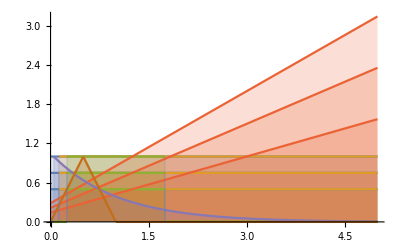

```mathematica
Plot[{xis[t,{0.5,.75,1}],step[t,.125,{0.5,.75,1}],rect[t,0.25,1.5,{0.5,.75,1}],ramp[t,.5,1.75,{0.5,.75,1}],exp[t,-0.05,1.0,3],triang[t,.00025,1.0,3]},{t,0,5},Filling->Axis]
```

#### Modeling

```mathematica
variablesconditioning1[lista1_,value_]:=Table[lista1[[n]][value],{n,1,Length[lista1]}]
variablesconditioning2[lista1_,lista2_]:=Table[lista1[[n]]==lista2[[n]],{n,1,Length[lista1]}]
fusionvariablesandmodels[variables_]:=Flatten[variables]
eqsfunctionstructure[variables_,models_]:=Flatten[variablesconditioning2[variables,models]]
```

```mathematica
unitQuati[]
```

```mathematica
px[t],py[t],pz[t]
```

```mathematica
transl=.;
rot=.;
veloc=.;
omega=.;
```

```mathematica
eqs=.;cis=.;eqssystem=.;

Clear[forcecmds,momentcmds]
translation={px,py,pz};
rotation={ϕ,θ,ψ};
velocities={u,v,w};
angrates={p,q,r};
(*transl=variablesconditioning1[translation,t];
rot=variablesconditioning1[rotation,t];
veloc=variablesconditioning1[velocities,t];
omega=variablesconditioning1[angrates,t];*)

translation={px,py,pz};rotation={ϕ,θ,ψ};velocities={u,v,w};angrates={p,q,r};Qtransf={q1,q2,q3,q4};
depvariables={translation,rotation,velocities,angrates,Qtransf};
```

```mathematica
modeling[depvarsmagnitude_,independentvar_,inertia_,force_,moment_,psithetaphiMatrix_]:=Block[{variablesconditioning1,variablesconditioning2,fusionvariablesandmodels,eqsfunctionstructure,MountingofVariables,transl,rot,veloc,omega,quaternion,InertialTensor,Ixy,Ixz,Iyx,Iyy,Iyz,Izx,Izy,Izz,mass,m,grav,g,forces,
moments,Tpsithetaphi,TAtoB,CAtoB,cayley,trans,accelerationmodel,rotationratemodel,velocmodel,angratemodel,quaternionderivative,models,vars,eqs},
(*Variables Conditioning Functions*)
variablesconditioning1[lista1_,value_]:=Table[lista1[[n]][value],{n,1,Length[lista1]}];variablesconditioning2[lista1_,lista2_]:=Table[lista1[[n]]==lista2[[n]],{n,1,Length[lista1]}];fusionvariablesandmodels[variables_]:=Flatten[variables];eqsfunctionstructure[variables_,models_]:=Flatten[variablesconditioning2[variables,models]];MountingofVariables[varsmagnitude_]:=If[Length[varsmagnitude]==4,{transl=variablesconditioning1[varsmagnitude[[1]],t],rot=variablesconditioning1[varsmagnitude[[2]],t],veloc=variablesconditioning1[varsmagnitude[[3]],t],omega=variablesconditioning1[varsmagnitude[[4]],t]},{transl=variablesconditioning1[varsmagnitude[[1]],t],rot=variablesconditioning1[varsmagnitude[[2]],t],veloc=variablesconditioning1[varsmagnitude[[3]],t],omega=variablesconditioning1[varsmagnitude[[4]],t],quaternion=variablesconditioning1[varsmagnitude[[5]],t]}];
(*Variables Conditioning  Processing*)
MountingofVariables[depvarsmagnitude];
(*Inertia*)
{{Ixx,Ixy,Ixz},{Iyx,Iyy,Iyz},{Izx,Izy,Izz}}=inertia;
InertialTensor={{Ixx,Ixy,Ixz},{Iyx,Iyy,Iyz},{Izx,Izy,Izz}};
(*Mass*)
(*mass=.;*)
mass=m;
(*Gravity*)
(*g=.;*)grav={0,0,-g};
(*Forces and Moments*)
forces=force;moments=moment;
(*Tpsithetaphi={{1,Cos[rot[[1]]] Tan[rot[[2]]],-Sin[rot[[1]]] Tan[rot[[2]]]},{0,Cos[rot[[1]]],-Sin[rot[[1]]]},{0,Sin[rot[[1]]/Cos[rot[[2]]]],Cos[rot[[1]]]/Cos[rot[[2]]]}};*)Tpsithetaphi=psithetaphiMatrix;TAtoB=TaitBryan[rot[[1]],rot[[2]],rot[[3]]];CAtoB=quatNot[quatNot[unitQuati[x,rot[[1]]],PM].quatNot[unitQuati[y,rot[[2]]],PM].unitQuati[z,rot[[3]]],Cayley];cayley=quatNot[{q1,q2,q3,q4},Cayley];
trans[transformationoption_(*"Q" quaternion or "T" transformation*)]:=If[transformationoption=="Q",CAtoB,TAtoB];
(*trans[transformationoption_(*"Q" quaternion or "T" transformation*)]:=If[transformationoption=="Q",quatNot[quatNot[unitQuati[x,rot[[1]]],PM].quatNot[unitQuati[y,rot[[2]]],PM].unitQuati[z,rot[[3]]],Cayley],TaitBryan[rot[[1]],rot[[2]],rot[[3]]]];
Qpsithetaphi=TMorQuaternion[Tpsithetaphi,QN];
Cpsithetaphi=quatNot[Qpsithetaphi,Cayley];
TpsithetaphiCayley=quatNot[Tpsithetaphi,PM];*)
(*rotationratemodel=(Inverse[InertialTensor].moment)-Inverse[InertialTensor].(crossvector[omega,InertialTensor.omega]);*)
(*accelerationmodel=TAtoB.(force/mass)- (crossvector[veloc,omega]-grav);*)
rotationratemodel=(Inverse[InertialTensor].moment)-Inverse[InertialTensor].(crossvector[omega,InertialTensor.omega]);
accelerationmodel[method_]:=trans[method].(force/mass)- (crossvector[veloc,omega]-grav);
(*velocmodel=Inverse[TaitBryan[rot[[1]],rot[[2]],rot[[3]]]].veloc;
velocmodel=TaitBryan[rot[[1]],rot[[2]],rot[[3]]].veloc;
velocmodel:=Inverse[TAtoB].veloc;*)
velocmodel[method_]:=Inverse[trans[method]].veloc;
angratemodel=Tpsithetaphi.omega;
quaternionderivative=QuatDeriv[{p,q,r,0},1];
vars=fusionvariablesandmodels[{Dt[veloc,t],Dt[omega,t],Dt[transl,t](*,Dt[rot,t]*),Dt[quaternion,t]}];
(*models=fusionvariablesandmodels[{accelerationmodel,rotationratemodel,velocmodel,angratemodel}];*)
models=fusionvariablesandmodels[{accelerationmodel["Q"],(*rotationratemodel,*)velocmodel["Q"],(*angratemodel,*)quaternionderivative}];
(*eqsfunctionstructure[vars,models]//MatrixForm*)
Do[
eqs =eqsfunctionstructure[vars,models],1];
Return[eqs] ]
```

```mathematica
fusionvariablesandmodels[{Dt[variablesconditioning1[depvariables[[1]],t],t],Dt[variablesconditioning1[depvariables[[2]],t],t],Dt[variablesconditioning1[depvariables[[3]],t],t](*,Dt[rot,t]*),Dt[variablesconditioning1[depvariables[[5]],t],t]}]
```

{px'[t],py'[t],pz'[t],ϕ'[t],θ'[t],ψ'[t],u'[t],v'[t],w'[t],q1'[t],q2'[t],q3'[t],q4'[t]}

```mathematica
If[transformationoption=="Q",CAtoB,TAtoB]
```

```mathematica
variablesconditioning1[depvariables[[1]],t]
```

{px[t],py[t],pz[t]}

```mathematica
Tpsithetaphi
```

{{1,{Cos[ϕ] Tan[t],Cos[θ] Tan[t],Cos[ψ] Tan[t]},{-Sin[ϕ] Tan[t],-Sin[θ] Tan[t],-Sin[ψ] Tan[t]}},{0,{Cos[ϕ],Cos[θ],Cos[ψ]},{-Sin[ϕ],-Sin[θ],-Sin[ψ]}},{0,{Sin[ϕ Sec[t]],Sin[θ Sec[t]],Sin[ψ Sec[t]]},{Cos[ϕ] Sec[t],Cos[θ] Sec[t],Cos[ψ] Sec[t]}}}

```mathematica
CAtoB
```

CAtoB

```mathematica
TaitBryan[ϕ,θ,ψ]
```

```mathematica
Inverse[TaitBryan[ϕ,θ,ψ]].variablesconditioning1[depvariables[[1]],t]//FullSimplify//MatrixForm
```

(Cos[θ] Cos[ψ] px[t]+Cos[ψ] Sin[θ] (Cos[ϕ] pz[t]+py[t] Sin[ϕ])+(-Cos[ϕ] py[t]+pz[t] Sin[ϕ]) Sin[ψ]
Cos[ψ] (Cos[ϕ] py[t]-pz[t] Sin[ϕ])+Cos[θ] px[t] Sin[ψ]+Sin[θ] (Cos[ϕ] pz[t]+py[t] Sin[ϕ]) Sin[ψ]
Cos[θ] Cos[ϕ] pz[t]-px[t] Sin[θ]+Cos[θ] py[t] Sin[ϕ])

```mathematica
variablesconditioning1[depvariables[[3]],t]
```

{u[t],v[t],w[t]}

```mathematica
(crossvector[variablesconditioning1[depvariables[[3]],t],{p[t],q[t],r[t]}]-{0,0,-g})//MatrixForm
```

(r[t] v[t]-q[t] w[t]
-r[t] u[t]+p[t] w[t]
g+q[t] u[t]-p[t] v[t])

```mathematica
fusionvariablesandmodels[{(1/m)TaitBryan[ϕ,θ,ψ].{fx,fy,fz}- (crossvector[variablesconditioning1[depvariables[[1]],t],{p[t],q[t],r[t]}]-{0,0,-g}),Inverse[TaitBryan[ϕ,θ,ψ]].variablesconditioning1[depvariables[[3]],t],QuatDeriv[{p,q,r,0},1],quatNot[quatNot[unitQuati[x,ϕ],PM].quatNot[unitQuati[y,θ],PM].unitQuati[z,ψ],Cayley]}]//FullSimplify//MatrixForm
```

(pz[t] q[t]-py[t] r[t]+(fx Cos[θ] Cos[ψ]-fz Sin[θ]+fy Cos[θ] Sin[ψ])/m
(-m p[t] pz[t]+m px[t] r[t]+fz Cos[θ] Sin[ϕ]+Cos[ϕ] (fy Cos[ψ]-fx Sin[ψ])+Sin[θ] Sin[ϕ] (fx Cos[ψ]+fy Sin[ψ]))/m
(-g m+fz Cos[θ] Cos[ϕ]+m p[t] py[t]-m px[t] q[t]+Sin[ϕ] (-fy Cos[ψ]+fx Sin[ψ])+Cos[ϕ] Sin[θ] (fx Cos[ψ]+fy Sin[ψ]))/m
Cos[θ] Cos[ψ] u[t]+(Cos[ψ] Sin[θ] Sin[ϕ]-Cos[ϕ] Sin[ψ]) v[t]+(Cos[ϕ] Cos[ψ] Sin[θ]+Sin[ϕ] Sin[ψ]) w[t]
Cos[θ] Sin[ψ] u[t]+Sin[θ] Sin[ψ] (Sin[ϕ] v[t]+Cos[ϕ] w[t])+Cos[ψ] (Cos[ϕ] v[t]-Sin[ϕ] w[t])
-Sin[θ] u[t]+Cos[θ] (Sin[ϕ] v[t]+Cos[ϕ] w[t])
1/2 (-q q3+p q4+q2 r)
1/2 (p q3+q q4-q1 r)
1/2 (q q1-p q2+q4 r)
1/2 (-p q1-q q2-q3 r)
Cos[θ] Cos[ψ]
Cos[θ] Sin[ψ]
-Sin[θ]
Cos[ψ] Sin[θ] Sin[ϕ]-Cos[ϕ] Sin[ψ]
Cos[ϕ] Cos[ψ]+Sin[θ] Sin[ϕ] Sin[ψ]
Cos[θ] Sin[ϕ]
Cos[ϕ] Cos[ψ] Sin[θ]+Sin[ϕ] Sin[ψ]
-Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[θ] Sin[ψ]
Cos[θ] Cos[ϕ])

```mathematica
QuatDeriv[{p,q,r,0},1]
```

{1/2 (-q q3+p q4+q2 r),1/2 (p q3+q q4-q1 r),1/2 (q q1-p q2+q4 r),1/2 (-p q1-q q2-q3 r)}

```mathematica
depvariables
```

{{px,py,pz},{ϕ,θ,ψ},{u,v,w},{p,q,r},{q1,q2,q3,q4}}

```mathematica
variablesconditioning1[depvariables[[5]],t]
```

{q1[t],q2[t],q3[t],q4[t]}

```mathematica
teste1={{0.8,0,0},{0,0.8,0},{0,0,0.8}};
teste2={{1,Cos[ϕ] Tan[θ],-Sin[ϕ] Tan[θ]},{0,Cos[ϕ],-Sin[ϕ]},{0,Sin[ϕ/Cos[θ]],Cos[ϕ]/Cos[θ]}};
```

```mathematica
teste1
```

```mathematica
modeling[depvariables,t,teste1,{fx,fy,fz},{tx,ty,tz},teste2]//FullSimplify
```

Part::partw: Part 11 of {(2 fy («1»))/m+(2 «2»«1»((Cos[«1»] Sin[«1»] Sin[«1»]-Cos[«1»] Cos[«1»] Sin[«1»]) (-Cos[«1»] Cos[«1»] Sin[«1»]+«1»)+«1»))/m+(fx (-(«1»)^2+(«1»)^2-(«1»)^2+(«1»+«1»)^2))/m-r[t] v[t]+q[t] w[t],(2 «2»«1»(«1»+«1»))/m+«5»,«6»,1/2 («1»),1/2 (-p q1-q q2-q3 r)} does not exist.

Part::partw: Part 12 of {(2 fy («1»))/m+(2 «2»«1»((Cos[«1»] Sin[«1»] Sin[«1»]-Cos[«1»] Cos[«1»] Sin[«1»]) (-Cos[«1»] Cos[«1»] Sin[«1»]+«1»)+«1»))/m+(fx (-(«1»)^2+(«1»)^2-(«1»)^2+(«1»+«1»)^2))/m-r[t] v[t]+q[t] w[t],(2 «2»«1»(«1»+«1»))/m+«5»,«6»,1/2 («1»),1/2 (-p q1-q q2-q3 r)} does not exist.

Part::partw: Part 13 of {(2 fy («1»))/m+(2 «2»«1»((Cos[«1»] Sin[«1»] Sin[«1»]-Cos[«1»] Cos[«1»] Sin[«1»]) (-Cos[«1»] Cos[«1»] Sin[«1»]+«1»)+«1»))/m+(fx (-(«1»)^2+(«1»)^2-(«1»)^2+(«1»+«1»)^2))/m-r[t] v[t]+q[t] w[t],(2 «2»«1»(«1»+«1»))/m+«5»,«6»,1/2 («1»),1/2 (-p q1-q q2-q3 r)} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{u'[t]==(-fz Sin[θ[t]]+Cos[θ[t]] (fx Cos[ψ[t]]+fy Sin[ψ[t]])-m r[t] v[t]+m q[t] w[t])/m,v'[t]==1/m(Cos[ϕ[t]] (fy Cos[ψ[t]]-fx Sin[ψ[t]])+Sin[ϕ[t]] (fz Cos[θ[t]]+Sin[θ[t]] (fx Cos[ψ[t]]+fy Sin[ψ[t]]))+m r[t] u[t]-m p[t] w[t]),w'[t]==1/m(-g m+fz Cos[θ[t]] Cos[ϕ[t]]+Sin[ϕ[t]] (-fy Cos[ψ[t]]+fx Sin[ψ[t]])+Cos[ϕ[t]] Sin[θ[t]] (fx Cos[ψ[t]]+fy Sin[ψ[t]])-m q[t] u[t]+m p[t] v[t]),Cos[ψ[t]] (Cos[θ[t]] u[t]+Sin[θ[t]] Sin[ϕ[t]] v[t])+(Cos[ϕ[t]] Cos[ψ[t]] Sin[θ[t]]+Sin[ϕ[t]] Sin[ψ[t]]) w[t]==Cos[ϕ[t]] Sin[ψ[t]] v[t]+p'[t],Cos[ϕ[t]] Cos[ψ[t]] v[t]+Sin[ψ[t]] (Cos[θ[t]] u[t]+Sin[θ[t]] (Sin[ϕ[t]] v[t]+Cos[ϕ[t]] w[t]))==Cos[ψ[t]] Sin[ϕ[t]] w[t]+q'[t],Sin[θ[t]] u[t]+r'[t]==Cos[θ[t]] (Sin[ϕ[t]] v[t]+Cos[ϕ[t]] w[t]),q q3+2 px'[t]==p q4+q2 r,p q3+q q4==q1 r+2 py'[t],q q1+q4 r==p q2+2 pz'[t],p q1+q q2+q3 r+2 q1'[t]==0,{(-fz Sin[θ[t]]+Cos[θ[t]] (fx Cos[ψ[t]]+fy Sin[ψ[t]])-m r[t] v[t]+m q[t] w[t])/m,1/m(Cos[ϕ[t]] (fy Cos[ψ[t]]-fx Sin[ψ[t]])+Sin[ϕ[t]] (fz Cos[θ[t]]+Sin[θ[t]] (fx Cos[ψ[t]]+fy Sin[ψ[t]]))+m r[t] u[t]-m p[t] w[t]),1/m(-g m+fz Cos[θ[t]] Cos[ϕ[t]]+Sin[ϕ[t]] (-fy Cos[ψ[t]]+fx Sin[ψ[t]])+Cos[ϕ[t]] Sin[θ[t]] (fx Cos[ψ[t]]+fy Sin[ψ[t]])-m q[t] u[t]+m p[t] v[t]),Cos[θ[t]] Cos[ψ[t]] u[t]+Cos[ψ[t]] Sin[θ[t]] Sin[ϕ[t]] v[t]-Cos[ϕ[t]] Sin[ψ[t]] v[t]+Cos[ϕ[t]] Cos[ψ[t]] Sin[θ[t]] w[t]+Sin[ϕ[t]] Sin[ψ[t]] w[t],Cos[θ[t]] Sin[ψ[t]] u[t]+Sin[θ[t]] Sin[ψ[t]] (Sin[ϕ[t]] v[t]+Cos[ϕ[t]] w[t])+Cos[ψ[t]] (Cos[ϕ[t]] v[t]-Sin[ϕ[t]] w[t]),-Sin[θ[t]] u[t]+Cos[θ[t]] (Sin[ϕ[t]] v[t]+Cos[ϕ[t]] w[t]),1/2 (-q q3+p q4+q2 r),1/2 (p q3+q q4-q1 r),1/2 (q q1-p q2+q4 r),1/2 (-p q1-q q2-q3 r)}⟦11⟧==q2'[t],{(-fz Sin[θ[t]]+Cos[θ[t]] (fx Cos[ψ[t]]+fy Sin[ψ[t]])-m r[t] v[t]+m q[t] w[t])/m,1/m(Cos[ϕ[t]] (fy Cos[ψ[t]]-fx Sin[ψ[t]])+Sin[ϕ[t]] (fz Cos[θ[t]]+Sin[θ[t]] (fx Cos[ψ[t]]+fy Sin[ψ[t]]))+m r[t] u[t]-m p[t] w[t]),1/m(-g m+fz Cos[θ[t]] Cos[ϕ[t]]+Sin[ϕ[t]] (-fy Cos[ψ[t]]+fx Sin[ψ[t]])+Cos[ϕ[t]] Sin[θ[t]] (fx Cos[ψ[t]]+fy Sin[ψ[t]])-m q[t] u[t]+m p[t] v[t]),Cos[θ[t]] Cos[ψ[t]] u[t]+Cos[ψ[t]] Sin[θ[t]] Sin[ϕ[t]] v[t]-Cos[ϕ[t]] Sin[ψ[t]] v[t]+Cos[ϕ[t]] Cos[ψ[t]] Sin[θ[t]] w[t]+Sin[ϕ[t]] Sin[ψ[t]] w[t],Cos[θ[t]] Sin[ψ[t]] u[t]+Sin[θ[t]] Sin[ψ[t]] (Sin[ϕ[t]] v[t]+Cos[ϕ[t]] w[t])+Cos[ψ[t]] (Cos[ϕ[t]] v[t]-Sin[ϕ[t]] w[t]),-Sin[θ[t]] u[t]+Cos[θ[t]] (Sin[ϕ[t]] v[t]+Cos[ϕ[t]] w[t]),1/2 (-q q3+p q4+q2 r),1/2 (p q3+q q4-q1 r),1/2 (q q1-p q2+q4 r),1/2 (-p q1-q q2-q3 r)}⟦12⟧==q3'[t],{(-fz Sin[θ[t]]+Cos[θ[t]] (fx Cos[ψ[t]]+fy Sin[ψ[t]])-m r[t] v[t]+m q[t] w[t])/m,1/m(Cos[ϕ[t]] (fy Cos[ψ[t]]-fx Sin[ψ[t]])+Sin[ϕ[t]] (fz Cos[θ[t]]+Sin[θ[t]] (fx Cos[ψ[t]]+fy Sin[ψ[t]]))+m r[t] u[t]-m p[t] w[t]),1/m(-g m+fz Cos[θ[t]] Cos[ϕ[t]]+Sin[ϕ[t]] (-fy Cos[ψ[t]]+fx Sin[ψ[t]])+Cos[ϕ[t]] Sin[θ[t]] (fx Cos[ψ[t]]+fy Sin[ψ[t]])-m q[t] u[t]+m p[t] v[t]),Cos[θ[t]] Cos[ψ[t]] u[t]+Cos[ψ[t]] Sin[θ[t]] Sin[ϕ[t]] v[t]-Cos[ϕ[t]] Sin[ψ[t]] v[t]+Cos[ϕ[t]] Cos[ψ[t]] Sin[θ[t]] w[t]+Sin[ϕ[t]] Sin[ψ[t]] w[t],Cos[θ[t]] Sin[ψ[t]] u[t]+Sin[θ[t]] Sin[ψ[t]] (Sin[ϕ[t]] v[t]+Cos[ϕ[t]] w[t])+Cos[ψ[t]] (Cos[ϕ[t]] v[t]-Sin[ϕ[t]] w[t]),-Sin[θ[t]] u[t]+Cos[θ[t]] (Sin[ϕ[t]] v[t]+Cos[ϕ[t]] w[t]),1/2 (-q q3+p q4+q2 r),1/2 (p q3+q q4-q1 r),1/2 (q q1-p q2+q4 r),1/2 (-p q1-q q2-q3 r)}⟦13⟧==q4'[t]}

quaternion=quatNot[{q1,q2,q3,q4}, Cayley];
phi=quaternion[[2]][[3]]/quaternion[[3]][[3]];
psi=quaternion[[1]][[2]]/quaternion[[1]][[1]];
theta=-quaternion[[1]][[3]]/Sqrt[(quaternion[[1]][[2]])^2+(quaternion[[1]][[1]])^2];

```mathematica
QuatDeriv[{p,q,r,0},1]//MatrixForm
```

(1/2 (-q q3+p q4+q2 r)
1/2 (p q3+q q4-q1 r)
1/2 (q q1-p q2+q4 r)
1/2 (-p q1-q q2-q3 r))

```mathematica
Tteste=TaitBryan[ϕ,θ,ψ];
cteste=quatNot[{q1,q2,q3,q4},Cayley];
```

```mathematica
Tteste//FullSimplify//MatrixForm
```

(Cos[θ] Cos[ψ] | Cos[θ] Sin[ψ] | -Sin[θ]
Cos[ψ] Sin[θ] Sin[ϕ]-Cos[ϕ] Sin[ψ] | Cos[ϕ] Cos[ψ]+Sin[θ] Sin[ϕ] Sin[ψ] | Cos[θ] Sin[ϕ]
Cos[ϕ] Cos[ψ] Sin[θ]+Sin[ϕ] Sin[ψ] | -Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[θ] Sin[ψ] | Cos[θ] Cos[ϕ])

```mathematica
testephi=Tteste[[2]][[3]]/Tteste[[3]][[3]]
```

Tan[ϕ]

```mathematica
testepsi=Tteste[[1]][[2]]/Tteste[[1]][[1]]
```

Tan[ψ]

```mathematica
testetheta=-Tteste[[1]][[3]]/Sqrt[(Tteste[[1]][[2]])^2+(Tteste[[1]][[1]])^2]
```

Sin[θ]/(√(Cos[θ]^2 Cos[ψ]^2+Cos[θ]^2 Sin[ψ]^2))

```mathematica
ArcTan
```

```mathematica
testetheta/.θ->π/6//FullSimplify
```

1/(√3)

```mathematica
ArcTan[1/(3^.5)]
```

0.523599

```mathematica
π/6//N
```

0.523599

```mathematica
Sqrt[(Tteste[[1]][[2]])^2+(Tteste[[1]][[1]])^2]
```

```mathematica
Sin[θ]/(√(Cos[θ]^2))
```

Sin[θ]/(√(Cos[θ]^2))

```mathematica
√(Cos[θ]^2)==Cos[θ]
```

√(Cos[θ]^2)==Cos[θ]

```mathematica
ArcTan[testetheta]
```

ArcTan[Sin[θ]/(√(Cos[θ]^2 Cos[ψ]^2+Cos[θ]^2 Sin[ψ]^2))]

```mathematica
deps={px,py,pz,ϕ,θ,ψ,u,v,w,p,q,r,q1,q2,q3,q4};
```

```mathematica
depvariables=.
```

```mathematica
depvariables[dataset_]:=Flatten[dataset];
```

```mathematica
Take[depvariables[deps],-4]
```

{q1,q2,q3,q4}

```mathematica
depvars[deps,4]
```

{px[t],py[t],pz[t],ϕ[t],θ[t],ψ[t],u[t],v[t],w[t],p[t],q[t],r[t]}

```mathematica
translation1={px,py,pz};rotation1={ϕ,θ,ψ};velocities1={u,v,w};angrates1={p,q,r};Qtransf1={q1,q2,q3,q4};
depvars1={translation1,rotation1,velocities1,angrates1};
depvars2={translation1,rotation1,velocities1,angrates1,Qtransf1};
```

```mathematica
variablesconditioning1[Qtransf1,t]
```

{q1[t],q2[t],q3[t],q4[t]}

```mathematica
depvars2
```

{{px,py,pz},{ϕ,θ,ψ},{u,v,w},{p,q,r},{q1,q2,q3,q4}}

```mathematica
depvars2//Length
```

5

```mathematica
testfnc[varsmagnitude_]:=If[Length[varsmagnitude]==4,{transl=variablesconditioning1[varsmagnitude[[1]],t],rot=variablesconditioning1[varsmagnitude[[2]],t],veloc=variablesconditioning1[varsmagnitude[[3]],t],omega=variablesconditioning1[varsmagnitude[[4]],t]},{transl=variablesconditioning1[varsmagnitude[[1]],t],rot=variablesconditioning1[varsmagnitude[[2]],t],veloc=variablesconditioning1[varsmagnitude[[3]],t],omega=variablesconditioning1[varsmagnitude[[4]],t],quaternion=variablesconditioning1[varsmagnitude[[5]],t]}]
```

```mathematica
testfnc[depvars1]
testfnc[depvars2]
```

{{px[t],py[t],pz[t]},{ϕ[t],θ[t],ψ[t]},{u[t],v[t],w[t]},{p[t],q[t],r[t]}}

{{px[t],py[t],pz[t]},{ϕ[t],θ[t],ψ[t]},{u[t],v[t],w[t]},{p[t],q[t],r[t]},{q1[t],q2[t],q3[t],q4[t]}}

```mathematica
rot
```

{ϕ[t],θ[t],ψ[t]}

#### forcemoment1[optionforce, optionmoment, indvar, Ftimeini, Mtimeini, Famplitude, Mamplitude, Fdeltat, Mdeltat] optionforce - Xis, Step, Rectangular, Ramp, Exponential or Triangular optionmoment - Xis, Step, Rectangular, Ramp, Exponential or Triangular indvar - independent variable Ftimeini - Time when start the force application Mtimeini - Time when start the moment application Famplitude - Force Amplitude Mamplitude - Moment Amplitude Fdeltat - Time interval Mdeltat - Time interval

```mathematica
forcemoment1[optionforce_,optionmoment_,indvar_,Ftimeini_,Mtimeini_,{forcex_,forcey_,forcez_},{torquex_,torquey_,torquez_},Fdeltat_,Mdeltat_]:=Block[{forcecmds,momentcmds,forceamp={forcex,forcey,forcez},momentamp={torquex,torquey,torquez},force,moment,length,xis,step,rect,ramp,exp,triang,fx,fy,fz,tx,ty,tz,forceX,forceStep,forceRect,forceRamp,forceExp,forceTriang,momentX,momentStep,momentRect,
momentRamp,momentExp,momentTriang,indv=indvar},
(*Clear[forcecmds,momentcmds];*)
(*FORCE AND MOMENT MODELS*)
xis[indvar,amplitude_]:=amplitude;
step[indvar,amplitude_,timeini_]:=Piecewise[{{0,Abs[indvar]<Abs[timeini]},{amplitude,indvar>=timeini}}];
rect[indvar,amplitude_,timeini_,deltat_]:=Piecewise[{{0,Abs[indvar]<timeini},{amplitude,timeini<=indvar<(timeini+deltat)},{0,(timeini+deltat)<indvar}}];
ramp[indvar,amplitude_,timeini_,deltat_]:=Piecewise[{{0,indvar<-timeini},{(amplitude/deltat) (indvar+timeini),-timeini<=indvar}}];
exp[indvar,amplitude_,timeini_]:=Piecewise[{{0,indvar<-timeini},{amplitude Exp[-amplitude (indvar+timeini)],-timeini<=indvar}}];
triang[indvar,amplitude_,timeini_,deltat_]:=Piecewise[{{((indvar-timeini)/(deltat/2)),timeini<=indvar<(timeini+(deltat/2))},{(((timeini+deltat)-indvar)/(deltat/2)),(timeini+(deltat/2))<=indvar<(timeini+deltat)}}];
Do[
(*FORCE AND MOMENT MODELS*)
(*FORCE MODELS*)
If[optionforce=="xis",forcecmds=forceamp(*xis[indvar,forceamp]*)];
If[optionforce=="step",forcecmds=Piecewise[{{0,Abs[indvar]<Abs[Ftimeini]},{forceamp,indvar>=Ftimeini}}](*step[indvar,forceamp,Ftimeini]*)];
If[optionforce=="rectangular",forcecmds=Piecewise[{{0,Abs[indvar]<Ftimeini},{forceamp,Ftimeini<=indvar<(Ftimeini+Fdeltat)},{0,(Ftimeini+Fdeltat)<indvar}}](*rect[indvar,forceamp,Ftimeini,Fdeltat]*)];
If[optionforce=="ramp",forcecmds=Piecewise[{{0,indvar<-Ftimeini},{(forceamp/Fdeltat) (indvar+Ftimeini),-Ftimeini<=indvar}}](*ramp[indvar,forceamp,Ftimeini,Fdeltat]*)];
If[optionforce=="exponential",forcecmds=Piecewise[{{0,indvar<-Ftimeini},{forceamp Exp[-forceamp (indvar+Ftimeini)],-Ftimeini<=indvar}}](*exp[indvar,forceamp,Ftimeini]*)];
If[optionforce=="triangular",forcecmds=Piecewise[{{((indvar-Ftimeini)/(Fdeltat/2)),Ftimeini<=indvar<(Ftimeini+(Fdeltat/2))},{(((Ftimeini+Fdeltat)-indvar)/(Fdeltat/2)),(Ftimeini+(Fdeltat/2))<=indvar<(Ftimeini+Fdeltat)}}](*triang[indvar,forceamp,Ftimeini,Fdeltat]*)];
(*MOMENT MODELS*)
If[optionmoment=="xis",momentcmds=forceamp(*xis[indvar,momentamp]*)];
If[optionmoment=="step",momentcmds=Piecewise[{{0,Abs[indvar]<Abs[Mtimeini]},{forceamp,indvar>=Mtimeini}}](*step[indvar,momentamp,Mtimeini]*)];
If[optionmoment=="rectangular",momentcmds=Piecewise[{{0,Abs[indvar]<Mtimeini},{forceamp,Mtimeini<=indvar<(Mtimeini+Mdeltat)},{0,(Mtimeini+Mdeltat)<indvar}}](*rect[indvar,momentamp,Mtimeini,Mdeltat]*)];
If[optionmoment=="ramp",momentcmds=Piecewise[{{0,indvar<-Mtimeini},{(forceamp/Mdeltat) (indvar+Mtimeini),-Mtimeini<=indvar}}](*ramp[indvar,momentamp,Mtimeini,Mdeltat]*)];
If[optionmoment=="exponential",momentcmds=Piecewise[{{0,indvar<-Mtimeini},{forceamp Exp[-forceamp (indvar+Mtimeini)],-Mtimeini<=indvar}}](*exp[indvar,momentamp,Mtimeini]*)];
If[optionmoment=="triangular",momentcmds=Piecewise[{{((indvar-Mtimeini)/(Mdeltat/2)),Mtimeini<=indvar<(Mtimeini+(Mdeltat/2))},{(((Mtimeini+Mdeltat)-indvar)/(Mdeltat/2)),(Mtimeini+(Mdeltat/2))<=indvar<(Mtimeini+Mdeltat)}}](*triang[indvar,momentamp,Mtimeini,Mdeltat]*)]
(*force=forcecmds;
moment=momentcmds*),1];
Return[{forcecmds,momentcmds}] (*to see all grid points*)]
```

```mathematica
force1[rectangular,t,.125,{fx,fy,fz},0.5]
```

forcecmds

forcemoment1[optionforce_,optionmoment_,indvar_,Ftimeini_,Mtimeini_,{forcex_,forcey_,forcez_},{torquex_,torquey_,torquez_},Fdeltat_,Mdeltat_]

```mathematica
forcemoment1[xis,xis,t,.125,.125,{1,1,1},{1,1,1},.5,.5]
```

{forcecmds,momentcmds}

force1[optionforce_, indvar_, Ftimeini_, {forcex_, forcey_, forcez_}, Fdeltat_] := Block[{forcecmds, forceamp = {forcex, forcey, forcez}, force, length, xis, step, rect, ramp, exp, triang, fx, fy, fz, forceX, forceStep, forceRect, forceRamp, forceExp, forceTriang, indv = indvar},
  Clear[forcecmds];
  (*FORCE AND MOMENT MODELS*)
  xis[indvar, amplitude_] := amplitude; 
  step[indvar, amplitude_, timeini_] := Piecewise[{{0, Abs[indvar] < Abs[timeini]}, {amplitude, indvar >= timeini}}];
  rect[indvar, amplitude_, timeini_, deltat_] := Piecewise[{{0, Abs[indvar] < timeini}, {amplitude, timeini <= indvar < (timeini + deltat)}, {0, (timeini + deltat) < indvar}}];
  ramp[indvar, amplitude_, timeini_, deltat_] := Piecewise[{{0, indvar < -timeini}, {(amplitude/deltat) (indvar + timeini), -timeini <= indvar}}];
  exp[indvar, amplitude_, timeini_] := Piecewise[{{0, indvar < -timeini}, {amplitude Exp[-amplitude (indvar + timeini)], -timeini <= indvar}}];
  triang[indvar, amplitude_, timeini_, deltat_] := Piecewise[{{((indvar - timeini)/(deltat/2)), timeini <= indvar < (timeini + (deltat/2))}, {(((timeini + deltat) - indvar)/(deltat/2)), (timeini + (deltat/2)) <= indvar < (timeini + deltat)}}];
  forceX = xis[indv, forceamp];
  forceStep = step[indv, forceamp, Ftimeini];
  forceRect = rect[indv, forceamp, Ftimeini, Fdeltat];
  forceRamp = ramp[indv, forceamp, Ftimeini, Fdeltat];
  forceExp = exp[indv, forceamp, Ftimeini];
  forceTriang = triang[indv, forceamp, Ftimeini, Fdeltat];
  Do[
   (*FORCE AND MOMENT MODELS*)
   (*FORCE MODELS*)
   If[optionforce == "xis", forcecmds = forceX];
   If[optionforce == "step", forcecmds = forceStep ];
   If[optionforce == "rectangular", forcecmds = forceRect];
   If[optionforce == "ramp", forcecmds = forceRamp];
   If[optionforce == "exponential", forcecmds = forceExp];
   If[optionforce == "triangular", forcecmds = forceTriang];
   force = forcecmds, 1];
  Return[forcecmds] (*to see all grid points*)]

```mathematica
force1[rectangular,t,.125,{fx,fy,fz},0.5]
```

forcecmds

```mathematica
forcemoment1[optionforce_,optionmoment_,indvar_,Ftimeini_,Mtimeini_,Famplitude_,Mamplitude_,Fdeltat_,Mdeltat_]
```

forcemoment1[optionforce_,optionmoment_,indvar_,Ftimeini_,Mtimeini_,Famplitude_,Mamplitude_,Fdeltat_,Mdeltat_]

#### Input Functions xis[t, amplitude] step[t , timeini, amplitude] rect[t, timeini, deltat, amplitude] ramp[t, timeini, deltat, amplitude] exp[t, timeini, alpha, amplitude] triang[t, timeini, deltat, amplitude] --------------------------------------x------------------------------------------- t - Time of evaluate timeini - Time when start the function application deltat - discretization of Time interval amplitude - Signal amplitude

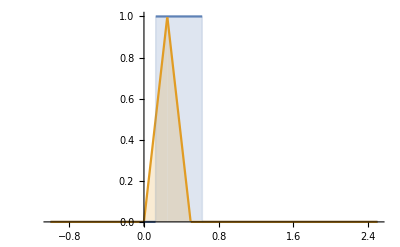

```mathematica
cmds1[t_,amplitude_]:=rect[t,.125,.5,amplitude]
cmds2[t_,amplitude_]:=triang[t,.125-.125,.5,amplitude]
Plot[{cmds1[t,1],cmds2[t,1]},{t,-1,2.5},PlotRange->All,Filling->Axis]
```

#### modeling1(depvars,indvar,{mass,gravity,Inertia,params},eqs0,transformations,commands) eqs,depvars,indvar,{mass,gravity,Inertia,params},eqs0,transformations,commands

```mathematica
transl=;
rot=;
```

```mathematica
transformation1=FullSimplify[Inverse[TaitBryan[rot[[1]],rot[[2]],rot[[3]]]]];
transformation2={{1,0,0},{0,Cos[rot[[1]]],-Sin[rot[[1]]]},{-Sin[rot[[2]]],Cos[rot[[2]]] Sin[rot[[1]]],Cos[rot[[2]]] Cos[rot[[3]]]}};
transformation={transformation1,transformation2};
```

Part::partd: Part specification rot⟦1⟧ is longer than depth of object.

Part::partd: Part specification rot⟦2⟧ is longer than depth of object.

Part::partd: Part specification rot⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rot⟦1⟧ is longer than depth of object.

Part::partd: Part specification rot⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
modeling1[depvars_,indvar_,{mass_,gravity_,Inertia_,params_},eqs0_,transformations_,commands_]:=Block[{cis,forcevector,momentvector,accelerationmodel,rotationratemodel,velocmodel,angratemodel,fusionvariablesandmodels,models,eqsfunctionstructure,eqssystem,translation,rotation,velocities,angrates,transl,rot,veloc,omega,velocities,angrates,transl,Transformation=transformations,variablesconditioning1,variablesconditioning2,cmdsfx,cmdsfy,cmdsfz,cmdstx,cmdsty,cmdstz,InertiaTensor,Ixx,Ixy,Ixz,Iyx,Iyy,Iyz,Izx,Izy,Izz,vars=depvars,indv=indvar,varsChanging,varsChangeProc,ActualizingEqSys,tnew,eqs,eqssysplusic=Flatten[{eqs,eqs0}],cmds,input=Flatten[{params,commands},1],depvarsquanty=Length[depvars]},
(*PARAMETERS AND FORCES AND MOMENTS*)
{{Ixx,Ixy,Ixz},{Iyx,Iyy,Iyz},{Izx,Izy,Izz}}=Inertia;
InertiaTensor={{Ixx,Ixy,Ixz},{Iyx,Iyy,Iyz},{Izx,Izy,Izz}};

cmdsfx=Flatten[commands][[1]]; cmdsfy=Flatten[commands][[2]]; cmdsfz=Flatten[commands][[3]]; cmdstx=Flatten[commands][[1]]; cmdsty=Flatten[commands][[2]]; cmdstz=Flatten[commands][[3]];
variablesconditioning1[lista1_,value_]:=Table[lista1[[n]][value],{n,1,Length[lista1]}];
variablesconditioning2[lista1_,lista2_]:=Table[lista1[[n]]==lista2[[n]],{n,1,Length[lista1]}];
(*PARAMETERS AND FORCES AND MOMENTS*)
translation={depvars[[1]],depvars[[2]],depvars[[3]]};
rotation={depvars[[4]],depvars[[5]],depvars[[6]]};
velocities={depvars[[7]],depvars[[8]],depvars[[9]]};
angrates={depvars[[10]],depvars[[11]],depvars[[12]]};
transl=variablesconditioning1[translation,indv];
rot=variablesconditioning1[rotation,indv];
veloc=variablesconditioning1[velocities,indv];
omega=variablesconditioning1[angrates,indv];
fusionvariablesandmodels[variables_]:=Flatten[variables];
eqsfunctionstructure[variables_,models_]:=Flatten[variablesconditioning2[variables,models]];
forcevector={cmdsfx,cmdsfy,cmdsfz};
momentvector={cmdstx,cmdsty,cmdstz};
accelerationmodel=(forcevector/mass)- (crossvector[veloc,omega]+gravity);
rotationratemodel=(Inverse[InertiaTensor].momentvector)-Inverse[InertiaTensor].(crossvector[omega,InertiaTensor.omega]);
velocmodel=Transformation[[1]].veloc;
angratemodel=Transformation[[2]].omega;
(*LOOP*)
Do[
vars=fusionvariablesandmodels[{Dt[veloc,indv],Dt[omega,indv],Dt[transl,indv],Dt[rot,indv]}];
models=fusionvariablesandmodels[{accelerationmodel,rotationratemodel,velocmodel,angratemodel}];
eqs =eqsfunctionstructure[vars,models],1];
Return[eqs] (*to see all grid points*)]
```

```mathematica
eqs
```

eqs

#### ivpPlant1 - ivpPlant1[eqs_,depvars_,indvar_,params_,commands_,{t0_,tn_},eqs0_,steps_]

```mathematica
ivpPlant1[eqs_,depvars_,indvar_,params_,commands_,{t0_,tn_},eqs0_,steps_]:=Block[{eqssys=eqs,vars=depvars,indv=indvar,told=t0,sollist={Flatten[{t0,If[Length[depvars]>1,Table[eqs0[[;;,2]][[n]],{n,Length[eqs0]}],eqs0[[1]][[2]]]}]}(*  Allocating the first value of dataset in sollist *),finalstate={},h=((tn-t0)/steps),solverkernel,solverkernel1,ptsSolution,ptsSolution1,varsChanging,varsChangeProc,ActualizingEqSys,tnew,eqssysplusic=Flatten[{eqs,eqs0}],cmds,input=Flatten[{params,commands},1],depvarsquanty=Length[depvars]},
varsChanging[{varA_,varB_}]:=varA->varB;
varsChangeProc[changing_]:=Map[varsChanging,changing];
ActualizingEqSys[fnc_,changing_]:=ReplaceAll[fnc,varsChangeProc[changing]];
(*ActualizingEqSys[eqssysplusic,input];*)
(* Kernel Function of solution *)
solverkernel1=Flatten[NDSolve[ActualizingEqSys[eqssysplusic,input],vars,{indv,t0,tn}]];
solverkernel[var_]:=Extract[solverkernel1,{var,2}];
(*Generator Function of Points Solution*)
ptsSolution1=Map[solverkernel,Range[Length[Flatten[{vars}]]]];
ptsSolution[time_]:=Through[ptsSolution1[time]];
(* Look of solution *)
Do[
tnew=told+h;
sollist=Append[sollist,Flatten[{tnew,ptsSolution[tnew]}]];
told=tnew,{steps}];
Return[{sollist,Append[finalstate,ptsSolution[tn]],eqssysplusic}] (*to see all grid points*)]
```

#### ivpPlant2 - ivpPlant2[eqs_,depvars_,indvar_,{t0_,tn_},eqs0_,steps_]

```mathematica
ivpPlant2[eqs_,depvars_,indvar_,{t0_,tn_},eqs0_,steps_]:=Block[{eqssys=eqs,vars=depvars,indv=indvar,told=t0,sollist={Flatten[{t0,If[Length[depvars]>1,Table[eqs0[[;;,2]][[n]],{n,Length[eqs0]}],eqs0[[1]][[2]]]}]}(*  Allocating the first value of dataset in sollist *),finalstate={},h=((tn-t0)/steps),solverkernel,solverkernel1,ptsSolution,ptsSolution1,tnew,eqssysplusic=Flatten[{eqs,eqs0}],depvarsquanty=Length[depvars]},
(* Kernel Function of solution *)
solverkernel1=Flatten[NDSolve[eqssysplusic,vars,{indv,t0,tn}]];
solverkernel[var_]:=Extract[solverkernel1,{var,2}];
(*Generator Function of Points Solution*)
ptsSolution1=Map[solverkernel,Range[Length[Flatten[{vars}]]]];
ptsSolution[time_]:=Through[ptsSolution1[time]];
(* Look of solution *)
Do[
tnew=told+h;
sollist=Append[sollist,Flatten[{tnew,ptsSolution[tnew]}]];
told=tnew,{steps}];
Return[{sollist,Append[finalstate,ptsSolution[tn]],eqssysplusic}] (*to see all grid points*)]
```

```mathematica
(*   incluir função de substituição de params e commands nas equações antes da solução  *)
```

#### ivpPlant3 - ivpPlant3[eqs_,depvars_,indvar_,params_,commands_,{t0_,tn_},eqs0_,steps_] QuatDeriv( If entity is a pure vector quaternion, DerivativeOption is 1. Otherwise, it is 2.) (in progressing)

ivpPlant3[eqs_, depvars_, indvar_, params_, commands_, {t0_, tn_}, eqs0_, steps_] := Block[{eqssys = eqs, vars = depvars, indv = indvar, told = t0, sollist = {Flatten[{t0, If[Length[depvars] > 1, Table[eqs0[[;; , 2]][[n]], {n, Length[eqs0]}], eqs0[[1]][[2]]]}]}(*  Allocating the first value of dataset in sollist *), finalstate = {}, h = ((tn - t0)/steps), solverkernel, solverkernel1, ptsSolution, ptsSolution1, varsChanging, varsChangeProc, ActualizingEqSys, tnew, eqssysplusic = Flatten[{eqs, eqs0}], cmds, input = Flatten[{params, commands}, 1], depvarsquanty = Length[depvars]},
  (* Conditioning the Variables *)
  varsChanging[{varA_, varB_}] := varA -> varB;
  varsChangeProc[changing_] := Map[varsChanging, changing];
  ActualizingEqSys[fnc_, changing_] := ReplaceAll[fnc, varsChangeProc[changing]];
  (* Transforming the vectors in the pure vectors quaternions *)
  
  (* Kernel Function of solution *)
  solverkernel1 = Flatten[NDSolve[ActualizingEqSys[eqssysplusic, input], vars, {indv, t0, tn}]];
  solverkernel[var_] := Extract[solverkernel1, {var, 2}];
  (*Generator Function of Points Solution*)
  ptsSolution1 = Map[solverkernel, Range[Length[Flatten[{vars}]]]];
  ptsSolution[time_] := Through[ptsSolution1[time]];
  (* Look of solution *)
  Do[
   tnew = told + h;
   sollist = Append[sollist, Flatten[{tnew, ptsSolution[tnew]}]];
   told = tnew, {steps}];
  Return[{sollist, Append[finalstate, ptsSolution[tn]], eqssysplusic}] (*to see all grid points*)]

### Example of application to the IVP model of plant

#### Example 1

{y'[x]==Cos[x+y[x]] y[x],y[0]==1}

0.136075 seconds

{0.0193018}

0.226271 seconds

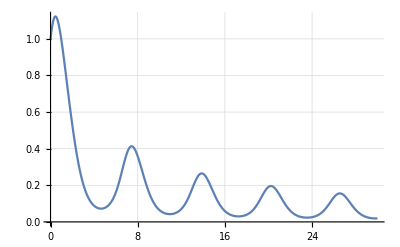

```mathematica
eqs=.;cis=.;eqssystem=.;
eqs={y'[x]==y[x]Cos[x+y[x]]};
cis={y[0]==1};
{time1,{sol,ci2,eqssystem}}=AbsoluteTiming[ivpPlant2[eqs,y,x,{0,30},cis,5000]];
{time,graf}=AbsoluteTiming[ListPlot[sol,Joined->True,PlotRange->All,GridLines->Automatic]];
eqssystem
time1"seconds"
ci2[[1]]
time"seconds"
graf
```

#### Example 2

{Sin[y[x]] y[x]+y''[x]==0,y[0]==1,y'[0]==0}

0.10532 seconds

{0.998999}

0.132869 seconds

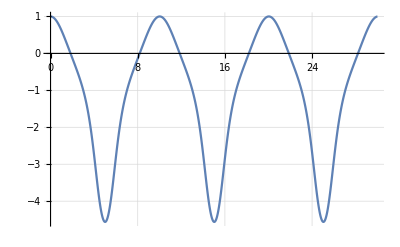

```mathematica
eqs=.;cis=.;eqssystem=.;
eqs={y''[x]+ Sin[y[x]]y[x]==0};
cis={y[0]==1,y'[0]==0};
{time1,{sol,ci2,eqssystem}}=AbsoluteTiming[ivpPlant2[eqs,y,x,{0,30},cis,5000]];
{time,graf}=AbsoluteTiming[ListPlot[sol,Joined->True,PlotRange->All,GridLines->Automatic]];
eqssystem
time1"seconds"
ci2[[1]]
time"seconds"
graf
```

#### Example 3

{x'[t]==-x[t]^2-params1 y[t],y'[t]==cmds1 x[t]-cmds2^3 y[t]^3,x[0]==1,y[0]==1}

0.343711 seconds

{-0.18161,-0.00751449}

0.232287 seconds

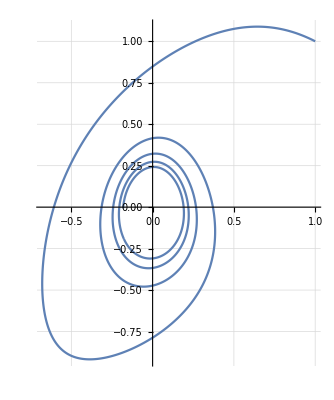

```mathematica
eqs=.;cis=.;eqssystem=.;
(*commands1=1;*)
(*params1=5;*)
eqs={x'[t]==-(y[t] params1)-x[t]^2,y'[t]==cmds1 x[t]-(cmds2 y[t])^3};
cis={x[0]==1,y[0]==1};
{time1,{sol,ci2,eqssystem}}=AbsoluteTiming[ivpPlant1[eqs,{x,y},t,{{params1,1}},{{cmds1,2},{cmds2,1}},{0,20},cis,10000]];
{time,graf}=AbsoluteTiming[ListPlot[Transpose[{Transpose[sol][[2]],Transpose[sol][[3]]}],Joined->True,PlotRange->All,AspectRatio->Full,GridLines->Automatic]];
eqssystem
time1"seconds"
ci2[[1]]
time"seconds"
graf
```

#### Example 4

Inclinação da rampa: π/4

step(t) = Piecewise[{{0, |t|< |δ|}, {1, t≥δ}, {0, True}}]

rect(t) = Piecewise[{{0, |t|<t1}, {1, t1≤t<t2}, {0, True}}]

Inclinação da rampa: π/4

ramp(t) = Piecewise[{{0, |t|<t1}, {tg(α)(t+t1), t1≤t}, {0, True}}]
triang(t) =Piecewise[{{(2 (0.125-t1))/ΔT, t1≤0.125<t1+ΔT/2}, {(2 (-0.125+t1+ΔT))/ΔT, t1+ΔT/2≤0.125<t1+ΔT}, {0, True}}]
https://geokrigagem.com.br/distribuicao-triangular/
https://www.wikiwand.com/pt/Fun%C3%A7%C3%A3o_triangular
https://www.researchgate.net/figure/Figura-31-Funcao-de-Pertinencia-Triangular-Fuzzy_fig6_317670946

```mathematica
xis[t_,amplitude_]:=amplitude
step[t_,timeini_,amplitude_]:=Piecewise[{{0,Abs[t]<Abs[timeini]},{amplitude,t>=timeini}}]  
rect[t_,timeini_,deltat_,amplitude_]:=Piecewise[{{0,Abs[t]<timeini},{amplitude,timeini<=t<(timeini+deltat)},{0,(timeini+deltat)<t}}]
ramp[t_,timeini_,deltat_,amplitude_]:=Piecewise[{{0,t<-timeini},{(amplitude/deltat) (t+timeini),-timeini<=t}}]
exp[t_,timeini_,alpha_,amplitude_]:=Piecewise[{{0,t<-timeini},{alpha Exp[-alpha (t+timeini)],-timeini<=t}}]
triang[t_,timeini_,deltat_,amplitude_]:=Piecewise[{{((t-timeini)/(deltat/2)),timeini<=t<(timeini+(deltat/2))},{(((timeini+deltat)-t)/(deltat/2)),(timeini+(deltat/2))<=t<(timeini+deltat)}}]
```

```mathematica
Clear[cmds1,cmds2]
```

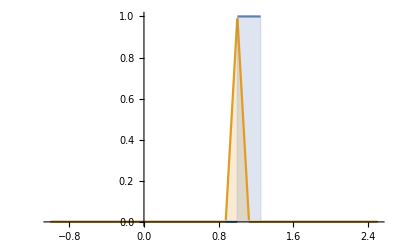

```mathematica
cmds1[t_,amplitude_]:=rect[t,1,.25,amplitude]
cmds2[t_,amplitude_]:=triang[t,1-.125,.25,amplitude]
Plot[{cmds1[t,1],cmds2[t,1]},{t,-1,2.5},PlotRange->All,Filling->Axis]
```

{x'[t]==-x[t]^2-params1 y[t],y'[t]==(Piecewise[{{0, Abs[t]<1}, {f1, 1≤t<1.25}, {0, True}}]) x[t]-(Piecewise[{{8. (-0.875+t), 0.875≤t<1.}, {8. (1.125-t), 1.≤t<1.125}, {0, True}}])^3 y[t]^3,x[0]==1,y[0]==1}

0.506103 seconds

{0.0211831,1.00111}

0.320131 seconds

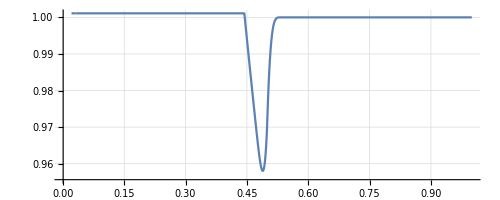

```mathematica
(*cmds1=.;cmds2=.;*)
eqs=.;cis=.;eqssystem=.;
(*commands1=1;*)
(*params1=5;*)
eqs={x'[t]==-(y[t] params1)-x[t]^2,y'[t]==cmds1[t,f1] x[t]-(cmds2[t,f2] y[t])^3};
cis={x[0]==1,y[0]==1};
{time1,{sol,ci2,eqssystem}}=AbsoluteTiming[ivpPlant1[eqs,{x,y},t,{{params1,.0010}},{{f1,.5},{f2,1}},{0,30},cis,10000]];
{time,graf}=AbsoluteTiming[ListPlot[Transpose[{Transpose[sol][[2]],Transpose[sol][[3]]}],Joined->True,PlotRange->All,AspectRatio->Full,GridLines->Automatic]];
eqssystem
time1"seconds"
ci2[[1]]
time"seconds"
graf
```

## Implementation of Solution

#### INERTIA

```mathematica
(* ivpPlant1[eqs_,depvars_,indvar_,params_,commands_,{t0_,tn_},eqs0_,steps_]  *)
(* implementar código do bloco de rascunho com foco no comando MapThread e no ivpPlant1*)
```

-Graphics-

#### SIMULATIONS

```mathematica
variablesconditioning1[lista1_,value_]:=Table[lista1[[n]][value],{n,1,Length[lista1]}]
variablesconditioning2[lista1_,lista2_]:=Table[lista1[[n]]==lista2[[n]],{n,1,Length[lista1]}]
fusionvariablesandmodels[variables_]:=Flatten[variables]
eqsfunctionstructure[variables_,models_]:=Flatten[variablesconditioning2[variables,models]]
```

#### Example 1

Modeling

Basic variables and constant

```mathematica
eqs=.;cis=.;eqssystem=.;
mass=3;
(*g=.;*)
grav={0,0,9.80665};
inertia={{0.8,0,0},{0,0.8,0},{0,0,0.8}};
```

Transformation

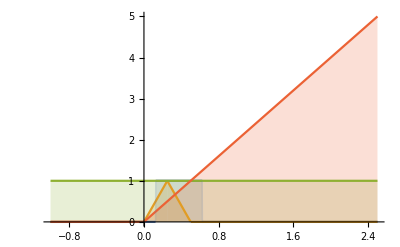

```mathematica
cmds1[t_,amplitude_]:=rect[t,.125,.5,amplitude]
cmds2[t_,amplitude_]:=triang[t,.125-.125,.5,amplitude]
cmds3[t_,amplitude_]:=xis[t,amplitude]
cmds4[t_,amplitude_]:=ramp[t,.125-.125,.5,amplitude]
Plot[{cmds1[t,1],cmds2[t,1],cmds3[t,1],cmds4[t,1]},{t,-1,2.5},PlotRange->All,Filling->Axis]
```

#### Example 1

-Graphics-

Modeling

```mathematica
eqs=.;cis=.;eqssystem=.;
Clear[forcecmds,momentcmds]
translation={px,py,pz};
rotation={ϕ,θ,ψ};
velocities={u,v,w};
angrates={p,q,r};
transl=variablesconditioning1[translation,t];
rot=variablesconditioning1[rotation,t];
veloc=variablesconditioning1[velocities,t];
omega=variablesconditioning1[angrates,t];
{{Ixx,Ixy,Ixz},{Iyx,Iyy,Iyz},{Izx,Izy,Izz}}={{0.8,0,0},{0,0.8,0},{0,0,0.8}};
InertialTensor={{Ixx,Ixy,Ixz},{Iyx,Iyy,Iyz},{Izx,Izy,Izz}};
(*mass=.;*)
mass=m;
(*g=.;*)
grav={0,0,-g};
force={fx,fy,fz};
moment={tx,ty,tz};
(*forcecmds[t_,for_]:=cmds3[t,for];(*1[t,for], 2[t,for], 3[t,for], 4[t,for]*)
momentcmds[t_,mom_]:=cmds3[t,mom];(*1[t,for], 2[t,for], 3[t,for], 4[t,for]*)
force={forcecmds[t,fx],forcecmds[t,fy],forcecmds[t,fz]};
moment={momentcmds[t,tx],momentcmds[t,ty],momentcmds[t,tz]};*)
(*force={forcecmds[t,fx],forcecmds[t,fy],forcecmds[t,fz]};
moment={momentcmds[t,tx],momentcmds[t,ty],momentcmds[t,tz]};*)
Tpsithetaphi={{1,Cos[rot[[1]]] Tan[rot[[2]]],-Sin[rot[[1]]] Tan[rot[[2]]]},{0,Cos[rot[[1]]],-Sin[rot[[1]]]},{0,Sin[rot[[1]]/Cos[rot[[2]]]],Cos[rot[[1]]]/Cos[rot[[2]]]}};
TAtoB=TaitBryan[rot[[1]],rot[[2]],rot[[3]]];
(*Qpsithetaphi=TMorQuaternion[Tpsithetaphi,QN];*)
(*Cpsithetaphi=quatNot[Qpsithetaphi,Cayley];*)
(*TpsithetaphiCayley=quatNot[Tpsithetaphi,PM];*)
(*accelerationmodel=(force/mass)- (crossvector[veloc,omega]+grav);
rotationratemodel=(Inverse[InertialTensor].moment)-Inverse[InertialTensor].(crossvector[omega,InertialTensor.omega]);*)
accelerationmodel=TAtoB.(force/mass)- (crossvector[veloc,omega]-grav);
rotationratemodel=(Inverse[InertialTensor].moment)-Inverse[InertialTensor].(crossvector[omega,InertialTensor.omega]);
(*velocmodel=Inverse[TaitBryan[rot[[1]],rot[[2]],rot[[3]]]].veloc;*)
(*velocmodel=TaitBryan[rot[[1]],rot[[2]],rot[[3]]].veloc;*)
velocmodel=Inverse[TAtoB].veloc;
angratemodel=Tpsithetaphi.omega;
vars=fusionvariablesandmodels[{Dt[veloc,t],Dt[omega,t],Dt[transl,t],Dt[rot,t]}];
models=fusionvariablesandmodels[{accelerationmodel,rotationratemodel,velocmodel,angratemodel}];
(*eqsfunctionstructure[vars,models]//MatrixForm*)
eqs =eqsfunctionstructure[vars,models];
```

RASCUNHOS

```mathematica
force
```

{fx,fy,fz}

```mathematica
moment
```

{tx,ty,tz}

```mathematica
rot
```

{ϕ[t],θ[t],ψ[t]}

```mathematica
TaitBryan[rot[[1]],rot[[2]],rot[[3]]]//MatrixForm
```

(Cos[θ[t]] Cos[ψ[t]] | Cos[θ[t]] Sin[ψ[t]] | -Sin[θ[t]]
Cos[ψ[t]] Sin[θ[t]] Sin[ϕ[t]]-Cos[ϕ[t]] Sin[ψ[t]] | Cos[ϕ[t]] Cos[ψ[t]]+Sin[θ[t]] Sin[ϕ[t]] Sin[ψ[t]] | Cos[θ[t]] Sin[ϕ[t]]
Cos[ϕ[t]] Cos[ψ[t]] Sin[θ[t]]+Sin[ϕ[t]] Sin[ψ[t]] | -Cos[ψ[t]] Sin[ϕ[t]]+Cos[ϕ[t]] Sin[θ[t]] Sin[ψ[t]] | Cos[θ[t]] Cos[ϕ[t]])

```mathematica
Tpsithetaphi={{1,Cos[rot[[1]]] Tan[rot[[2]]],-Sin[rot[[1]]] Tan[rot[[2]]]},{0,Cos[rot[[1]]],-Sin[rot[[1]]]},{0,Sin[rot[[1]]/Cos[rot[[2]]]],Cos[rot[[1]]]/Cos[rot[[2]]]}};
```

```mathematica
Inverse[TAtoB]//FullSimplify//MatrixForm
```

(Cos[θ[t]] Cos[ψ[t]] | Cos[ψ[t]] Sin[θ[t]] Sin[ϕ[t]]-Cos[ϕ[t]] Sin[ψ[t]] | Cos[ϕ[t]] Cos[ψ[t]] Sin[θ[t]]+Sin[ϕ[t]] Sin[ψ[t]]
Cos[θ[t]] Sin[ψ[t]] | Cos[ϕ[t]] Cos[ψ[t]]+Sin[θ[t]] Sin[ϕ[t]] Sin[ψ[t]] | -Cos[ψ[t]] Sin[ϕ[t]]+Cos[ϕ[t]] Sin[θ[t]] Sin[ψ[t]]
-Sin[θ[t]] | Cos[θ[t]] Sin[ϕ[t]] | Cos[θ[t]] Cos[ϕ[t]])

```mathematica
TAtoB=TaitBryan[rot[[1]],rot[[2]],rot[[3]]];
```

```mathematica
(*Qpsithetaphi=TMorQuaternion[Tpsithetaphi,QN];*)
Qpsithetaphi=quatNot[unitQuati[x,ϕ],PM].quatNot[unitQuati[y,θ],PM].unitQuati[z,ψ];
PMQpsithetaphi=quatNot[Qpsithetaphi,PM];
Cpsithetaphi=quatNot[Qpsithetaphi,Cayley];
```

```mathematica
Cpsithetaphi
```

```mathematica
quatNot[{q1,q2,q3,q4},Cayley]//FullSimplify//MatrixForm
```

(q1^2-q2^2-q3^2+q4^2 | 2 q1 q2-2 q3 q4 | 2 (q1 q3+q2 q4)
2 (q1 q2+q3 q4) | -q1^2+q2^2-q3^2+q4^2 | 2 q2 q3-2 q1 q4
2 q1 q3-2 q2 q4 | 2 (q2 q3+q1 q4) | -q1^2-q2^2+q3^2+q4^2)

```mathematica
TMorQuaternion[Tpsithetaphi,QN];
```

```mathematica
PMQpsithetaphi.{p,q,r,0}//FullSimplify//MatrixForm
-quatNot[{p,q,r,0},PM].Qpsithetaphi//FullSimplify//MatrixForm
```

```mathematica
Cpsithetaphi=quatNot[Qpsithetaphi,Cayley];
```

```mathematica
TpsithetaphiCayley=quatNot[Tpsithetaphi,PM];
```

```mathematica
(1/2)quatNot[quatNot[unitQuati[x,ϕ],PM].quatNot[unitQuati[y,θ],PM].unitQuati[z,ψ],(*Qrepres*)PM].{p,q,r,0}//FullSimplify//MatrixForm
```

(1/2 (Sin[θ/2] (-Cos[ψ/2] (r Cos[ϕ/2]+q Sin[ϕ/2])+p Sin[ϕ/2] Sin[ψ/2])+Cos[θ/2] (-r Sin[ϕ/2] Sin[ψ/2]+Cos[ϕ/2] (p Cos[ψ/2]+q Sin[ψ/2])))
1/2 (Sin[θ/2] (p Cos[ψ/2] Sin[ϕ/2]+(-r Cos[ϕ/2]+q Sin[ϕ/2]) Sin[ψ/2])+Cos[θ/2] (r Cos[ψ/2] Sin[ϕ/2]+Cos[ϕ/2] (q Cos[ψ/2]-p Sin[ψ/2])))
1/2 (Cos[θ/2] (r Cos[ϕ/2] Cos[ψ/2]+Sin[ϕ/2] (-q Cos[ψ/2]+p Sin[ψ/2]))+Sin[θ/2] (r Sin[ϕ/2] Sin[ψ/2]+Cos[ϕ/2] (p Cos[ψ/2]+q Sin[ψ/2])))
1/2 (Cos[ϕ/2] (q Cos[ψ/2] Sin[θ/2]+(r Cos[θ/2]-p Sin[θ/2]) Sin[ψ/2])+Sin[ϕ/2] (-r Cos[ψ/2] Sin[θ/2]+Cos[θ/2] (p Cos[ψ/2]+q Sin[ψ/2]))))

```mathematica
Qpsithetaphi//FullSimplify//MatrixForm
```

(-Cos[θ/2] Cos[ψ/2] Sin[ϕ/2]+Cos[ϕ/2] Sin[θ/2] Sin[ψ/2]
-Cos[ϕ/2] Cos[ψ/2] Sin[θ/2]-Cos[θ/2] Sin[ϕ/2] Sin[ψ/2]
Cos[ψ/2] Sin[θ/2] Sin[ϕ/2]-Cos[θ/2] Cos[ϕ/2] Sin[ψ/2]
Cos[θ/2] Cos[ϕ/2] Cos[ψ/2]+Sin[θ/2] Sin[ϕ/2] Sin[ψ/2])

-Graphics-Gonzalez p23 
q = unitq_x*unitq_y*unitqz

#### a) Quaternion Function - quatNot( (portion1, portion2, portion3, portion4), (Qrepres, CJG, EUCNORM, INV, VP, SP, PM, Cayley, ALL) ) Qrepres - quaternion representation; CJG - quaternion conjugate; EUCNORM - Euclidean Norm; INV - inverse quaternion; VP - vector part; SP - scalar part; PM - product matrix; Cayley - Cayley matrix; and ALL - All elements.

Recovering CIS

```mathematica
cis=.;
cis=Flatten[{variablesconditioning2[variablesconditioning1[velocities,0],{0,0,0}],variablesconditioning2[variablesconditioning1[angrates,0],{0,0,0}],variablesconditioning2[variablesconditioning1[translation,0],{0,0,0}],variablesconditioning2[variablesconditioning1[rotation,0],{0,0,0}]}];
```

Solution - Time interval = 0s - 1s
CI1

```mathematica
cis1=.;
cis1=Flatten[{variablesconditioning2[variablesconditioning1[velocities,0],{0,0,0}],variablesconditioning2[variablesconditioning1[angrates,0],{0,0,0}],variablesconditioning2[variablesconditioning1[translation,0],{0,0,.25}],variablesconditioning2[variablesconditioning1[rotation,0],{0,0,0}]}];
```

(u'(t)==(fx cos(θ(t)) cos(ψ(t)))/m+(fy cos(θ(t)) sin(ψ(t)))/m-(fz sin(θ(t)))/m+q(t) w(t)-r(t) v(t)
v'(t)==(fx (sin(θ(t)) cos(ψ(t)) sin(ϕ(t))-sin(ψ(t)) cos(ϕ(t))))/m+(fy (sin(θ(t)) sin(ψ(t)) sin(ϕ(t))+cos(ψ(t)) cos(ϕ(t))))/m+(fz cos(θ(t)) sin(ϕ(t)))/m-p(t) w(t)+r(t) u(t)
w'(t)==(fx (sin(θ(t)) cos(ψ(t)) cos(ϕ(t))+sin(ψ(t)) sin(ϕ(t))))/m+(fy (sin(θ(t)) sin(ψ(t)) cos(ϕ(t))-cos(ψ(t)) sin(ϕ(t))))/m+(fz cos(θ(t)) cos(ϕ(t)))/m-g+p(t) v(t)-q(t) u(t)
p'(t)==1.25 tx+0.
q'(t)==1.25 ty+0.
r'(t)==1.25 tz+0.
px'(t)==(u(t) (cos(θ(t)) cos(ψ(t)) cos^2(ϕ(t))+cos(θ(t)) cos(ψ(t)) sin^2(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(v(t) (cos^2(θ(t)) sin(ψ(t)) (-cos(ϕ(t)))-sin^2(θ(t)) sin(ψ(t)) cos(ϕ(t))+sin(θ(t)) cos(ψ(t)) sin(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(w(t) (sin^2(θ(t)) sin(ψ(t)) sin(ϕ(t))+cos^2(θ(t)) sin(ψ(t)) sin(ϕ(t))+sin(θ(t)) cos(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))
py'(t)==(u(t) (cos(θ(t)) sin(ψ(t)) cos^2(ϕ(t))+cos(θ(t)) sin(ψ(t)) sin^2(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(v(t) (sin(θ(t)) sin(ψ(t)) sin(ϕ(t))+cos^2(θ(t)) cos(ψ(t)) cos(ϕ(t))+sin^2(θ(t)) cos(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(w(t) (cos^2(θ(t)) (-cos(ψ(t))) sin(ϕ(t))-sin^2(θ(t)) cos(ψ(t)) sin(ϕ(t))+sin(θ(t)) sin(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))
pz'(t)==(u(t) (-sin(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))-sin(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))-sin(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))-sin(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(v(t) (cos(θ(t)) cos^2(ψ(t)) sin(ϕ(t))+cos(θ(t)) sin^2(ψ(t)) sin(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(w(t) (cos(θ(t)) cos^2(ψ(t)) cos(ϕ(t))+cos(θ(t)) sin^2(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))
ϕ'(t)==p(t)+q(t) tan(θ(t)) cos(ϕ(t))-r(t) tan(θ(t)) sin(ϕ(t))
θ'(t)==q(t) cos(ϕ(t))-r(t) sin(ϕ(t))
ψ'(t)==q(t) sin(ϕ(t) sec(θ(t)))+r(t) sec(θ(t)) cos(ϕ(t))
u(0)==0
v(0)==0
w(0)==0
p(0)==0
q(0)==0
r(0)==0
px(0)==0
py(0)==0
pz(0)==0.25
ϕ(0)==0
θ(0)==0
ψ(0)==0)

{0.,0.,1.86002,0.,0.,0.,0.,0.,1.18001,0.,0.,0.}

0.228913 seconds

0.21589 seconds

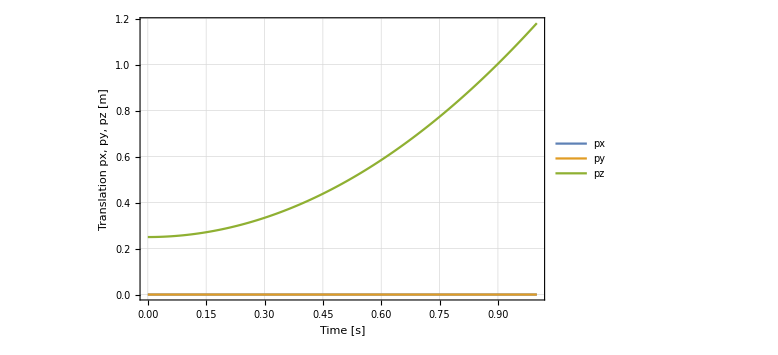
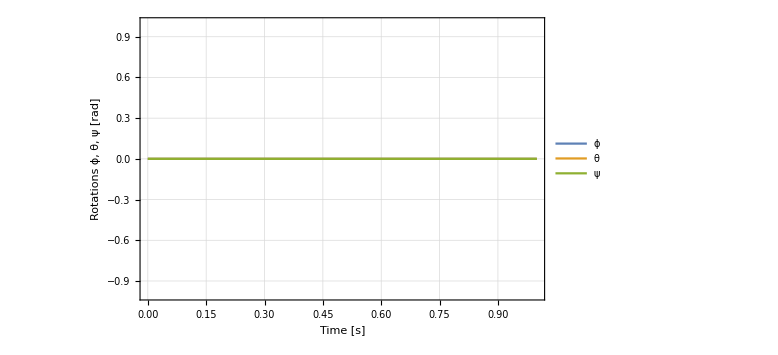
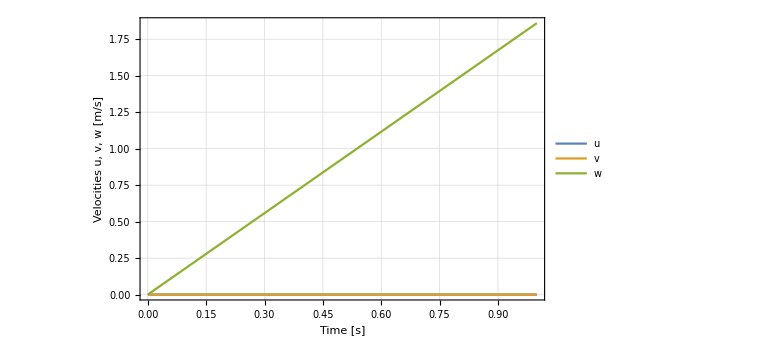
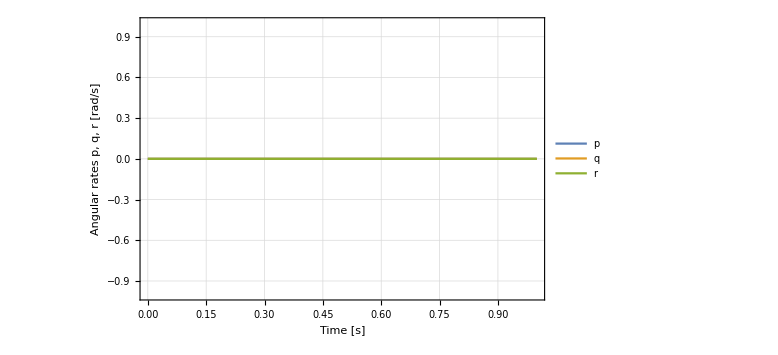
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
{time1,{sol,ci2,eqssystem}}=AbsoluteTiming[ivpPlant1[eqs,Flatten[{velocities,angrates,translation,rotation}],t,{{g,9.80665},{m,3}},{{fx,0},{fy,0},{fz,35},{tx,0},{ty,0},{tz,0}},{0,1},cis1,100]];
{{time1,graphposition},{time2,graphatitude}}={AbsoluteTiming[graphics2[sol,{"px [m]","py [m]","pz [m]"},1,{"Time [s]","Translation px, py, pz [m]"},{8,9,10}]],AbsoluteTiming[graphics2[sol,{"ϕ [rad]","θ [rad]","ψ [rad]"},1,{"Time [s]","Rotations ϕ, θ, ψ [rad]"},{11,12,13}]]};
graftranslationsvstime=graphics1[sol,{"px","py","pz"},1,{"Time [s]","Translation px, py, pz [m]"},{8,9,10}];
grafrotarionsvstime=graphics1[sol,{"ϕ","θ","ψ"},1,{"Time [s]","Rotations ϕ, θ, ψ [rad]"},{11,12,13}];
grafvelocityvstime=graphics1[sol,{"u","v","w"},1,{"Time [s]","Velocities u, v, w [m/s]"},{2,3,4}];
grafomegavstime=graphics1[sol,{"p","q","r"},1,{"Time [s]","Angular rates p, q, r [rad/s]"},{5,6,7}];
eqssystem//MatrixForm//TraditionalForm
ci2[[1]]
time1"seconds"
time2"seconds"
(*graphposition
graphatitude*)
grfcexerc1=Grid[Partition[{graftranslationsvstime,grafrotarionsvstime,grafvelocityvstime,grafomegavstime},2]]
graftranslationsvstime;
grafrotarionsvstime;
grafvelocityvstime;
grafomegavstime;
```

Solution - Time interval = 1s - 2s
CI2

```mathematica
3 9.80665 1.1
```

32.3619

```mathematica
cis2=.;
cis2=Flatten[{variablesconditioning2[variablesconditioning1[velocities,1],ci2[[1]][[1;;3]]],variablesconditioning2[variablesconditioning1[angrates,1],ci2[[1]][[4;;6]]],variablesconditioning2[variablesconditioning1[translation,1],ci2[[1]][[7;;9]]],variablesconditioning2[variablesconditioning1[rotation,1],ci2[[1]][[10;;12]]]}];
```

(u'(t)==(fx cos(θ(t)) cos(ψ(t)))/m+(fy cos(θ(t)) sin(ψ(t)))/m-(fz sin(θ(t)))/m+q(t) w(t)-r(t) v(t)
v'(t)==(fx (sin(θ(t)) cos(ψ(t)) sin(ϕ(t))-sin(ψ(t)) cos(ϕ(t))))/m+(fy (sin(θ(t)) sin(ψ(t)) sin(ϕ(t))+cos(ψ(t)) cos(ϕ(t))))/m+(fz cos(θ(t)) sin(ϕ(t)))/m-p(t) w(t)+r(t) u(t)
w'(t)==(fx (sin(θ(t)) cos(ψ(t)) cos(ϕ(t))+sin(ψ(t)) sin(ϕ(t))))/m+(fy (sin(θ(t)) sin(ψ(t)) cos(ϕ(t))-cos(ψ(t)) sin(ϕ(t))))/m+(fz cos(θ(t)) cos(ϕ(t)))/m-g+p(t) v(t)-q(t) u(t)
p'(t)==1.25 tx+0.
q'(t)==1.25 ty+0.
r'(t)==1.25 tz+0.
px'(t)==(u(t) (cos(θ(t)) cos(ψ(t)) cos^2(ϕ(t))+cos(θ(t)) cos(ψ(t)) sin^2(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(v(t) (cos^2(θ(t)) sin(ψ(t)) (-cos(ϕ(t)))-sin^2(θ(t)) sin(ψ(t)) cos(ϕ(t))+sin(θ(t)) cos(ψ(t)) sin(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(w(t) (sin^2(θ(t)) sin(ψ(t)) sin(ϕ(t))+cos^2(θ(t)) sin(ψ(t)) sin(ϕ(t))+sin(θ(t)) cos(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))
py'(t)==(u(t) (cos(θ(t)) sin(ψ(t)) cos^2(ϕ(t))+cos(θ(t)) sin(ψ(t)) sin^2(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(v(t) (sin(θ(t)) sin(ψ(t)) sin(ϕ(t))+cos^2(θ(t)) cos(ψ(t)) cos(ϕ(t))+sin^2(θ(t)) cos(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(w(t) (cos^2(θ(t)) (-cos(ψ(t))) sin(ϕ(t))-sin^2(θ(t)) cos(ψ(t)) sin(ϕ(t))+sin(θ(t)) sin(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))
pz'(t)==(u(t) (-sin(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))-sin(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))-sin(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))-sin(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(v(t) (cos(θ(t)) cos^2(ψ(t)) sin(ϕ(t))+cos(θ(t)) sin^2(ψ(t)) sin(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(w(t) (cos(θ(t)) cos^2(ψ(t)) cos(ϕ(t))+cos(θ(t)) sin^2(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))
ϕ'(t)==p(t)+q(t) tan(θ(t)) cos(ϕ(t))-r(t) tan(θ(t)) sin(ϕ(t))
θ'(t)==q(t) cos(ϕ(t))-r(t) sin(ϕ(t))
ψ'(t)==q(t) sin(ϕ(t) sec(θ(t)))+r(t) sec(θ(t)) cos(ϕ(t))
u(1)==0.
v(1)==0.
w(1)==1.86002
p(1)==0.
q(1)==0.
r(1)==0.
px(1)==0.
py(1)==0.
pz(1)==1.18001
ϕ(1)==0.
θ(1)==0.
ψ(1)==0.)

{1.66667,0.,2.84068,0.,0.,0.,0.833333,0.,3.53036,0.,0.,0.}

0.220543 seconds

0.202829 seconds

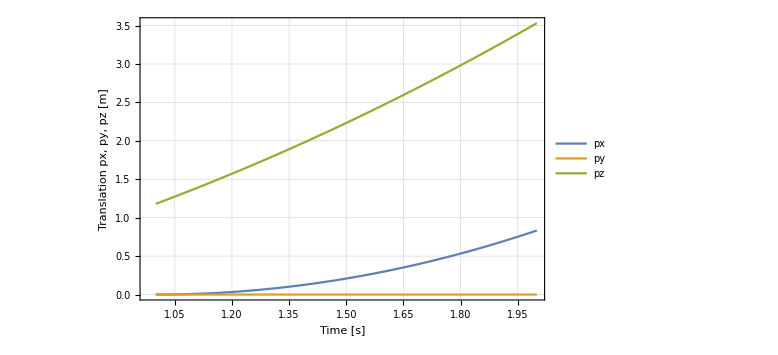
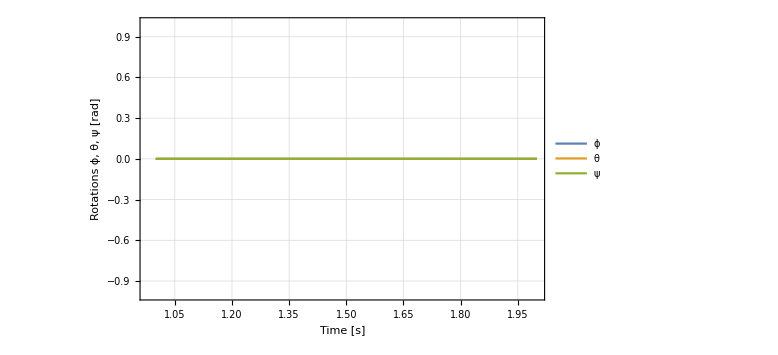
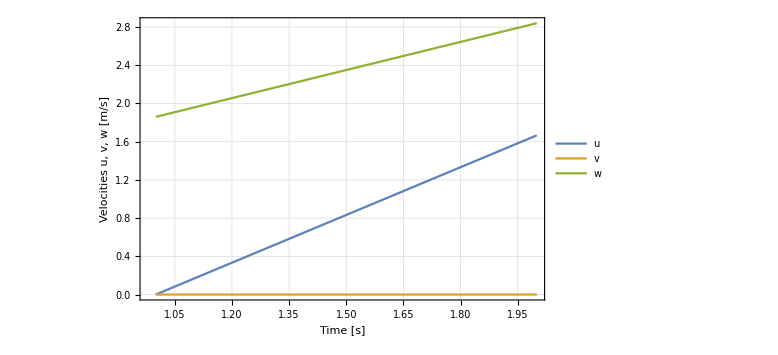
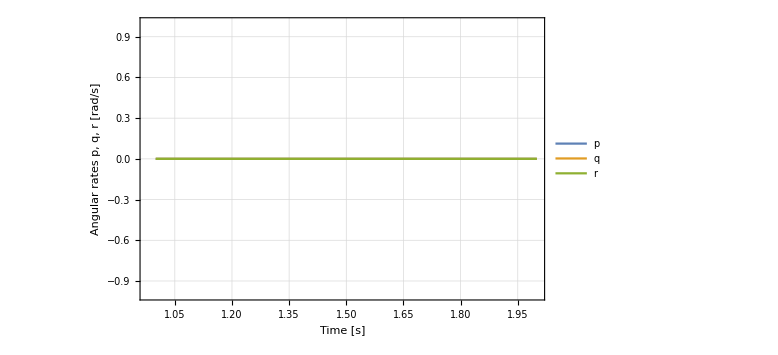
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
{time1,{sol,ci3,eqssystem}}=AbsoluteTiming[ivpPlant1[eqs,Flatten[{velocities,angrates,translation,rotation}],t,{{g,9.80665},{m,3}},{{fx,5},{fy,0},{fz,3 9.80665 1.1},{tx,0},{ty,0},{tz,0}},{1,2},cis2,100]];
{{time1,graphposition},{time2,graphatitude}}={AbsoluteTiming[graphics2[sol,{"px [m]","py [m]","pz [m]"},1,{"Time [s]","Translation px, py, pz [m]"},{8,9,10}]],AbsoluteTiming[graphics2[sol,{"ϕ [rad]","θ [rad]","ψ [rad]"},1,{"Time [s]","Rotations ϕ, θ, ψ [rad]"},{11,12,13}]]};
graftranslationsvstime=graphics1[sol,{"px","py","pz"},1,{"Time [s]","Translation px, py, pz [m]"},{8,9,10}];
grafrotarionsvstime=graphics1[sol,{"ϕ","θ","ψ"},1,{"Time [s]","Rotations ϕ, θ, ψ [rad]"},{11,12,13}];
grafvelocityvstime=graphics1[sol,{"u","v","w"},1,{"Time [s]","Velocities u, v, w [m/s]"},{2,3,4}];
grafomegavstime=graphics1[sol,{"p","q","r"},1,{"Time [s]","Angular rates p, q, r [rad/s]"},{5,6,7}];
eqssystem//MatrixForm//TraditionalForm
ci3[[1]]
time1"seconds"
time2"seconds"
(*grafveloc
grafvelocang*)
graftranslationsvstime;
grafrotarionsvstime;
grafvelocityvstime;
grafomegavstime;
grfcexerc2=Grid[Partition[{graftranslationsvstime,grafrotarionsvstime,grafvelocityvstime,grafomegavstime},2]]
```

Solution - Time interval = 2s - 3s
CI3

```mathematica
9.8066 3
```

29.4198

```mathematica
cis3=.;
cis3=Flatten[{variablesconditioning2[variablesconditioning1[velocities,2],ci3[[1]][[1;;3]]],variablesconditioning2[variablesconditioning1[angrates,2],ci3[[1]][[4;;6]]],variablesconditioning2[variablesconditioning1[translation,2],ci3[[1]][[7;;9]]],variablesconditioning2[variablesconditioning1[rotation,2],ci3[[1]][[10;;12]]]}];
```

(u'(t)==(fx cos(θ(t)) cos(ψ(t)))/m+(fy cos(θ(t)) sin(ψ(t)))/m-(fz sin(θ(t)))/m+q(t) w(t)-r(t) v(t)
v'(t)==(fx (sin(θ(t)) cos(ψ(t)) sin(ϕ(t))-sin(ψ(t)) cos(ϕ(t))))/m+(fy (sin(θ(t)) sin(ψ(t)) sin(ϕ(t))+cos(ψ(t)) cos(ϕ(t))))/m+(fz cos(θ(t)) sin(ϕ(t)))/m-p(t) w(t)+r(t) u(t)
w'(t)==(fx (sin(θ(t)) cos(ψ(t)) cos(ϕ(t))+sin(ψ(t)) sin(ϕ(t))))/m+(fy (sin(θ(t)) sin(ψ(t)) cos(ϕ(t))-cos(ψ(t)) sin(ϕ(t))))/m+(fz cos(θ(t)) cos(ϕ(t)))/m-g+p(t) v(t)-q(t) u(t)
p'(t)==1.25 tx+0.
q'(t)==1.25 ty+0.
r'(t)==1.25 tz+0.
px'(t)==(u(t) (cos(θ(t)) cos(ψ(t)) cos^2(ϕ(t))+cos(θ(t)) cos(ψ(t)) sin^2(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(v(t) (cos^2(θ(t)) sin(ψ(t)) (-cos(ϕ(t)))-sin^2(θ(t)) sin(ψ(t)) cos(ϕ(t))+sin(θ(t)) cos(ψ(t)) sin(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(w(t) (sin^2(θ(t)) sin(ψ(t)) sin(ϕ(t))+cos^2(θ(t)) sin(ψ(t)) sin(ϕ(t))+sin(θ(t)) cos(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))
py'(t)==(u(t) (cos(θ(t)) sin(ψ(t)) cos^2(ϕ(t))+cos(θ(t)) sin(ψ(t)) sin^2(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(v(t) (sin(θ(t)) sin(ψ(t)) sin(ϕ(t))+cos^2(θ(t)) cos(ψ(t)) cos(ϕ(t))+sin^2(θ(t)) cos(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(w(t) (cos^2(θ(t)) (-cos(ψ(t))) sin(ϕ(t))-sin^2(θ(t)) cos(ψ(t)) sin(ϕ(t))+sin(θ(t)) sin(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))
pz'(t)==(u(t) (-sin(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))-sin(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))-sin(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))-sin(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(v(t) (cos(θ(t)) cos^2(ψ(t)) sin(ϕ(t))+cos(θ(t)) sin^2(ψ(t)) sin(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(w(t) (cos(θ(t)) cos^2(ψ(t)) cos(ϕ(t))+cos(θ(t)) sin^2(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))
ϕ'(t)==p(t)+q(t) tan(θ(t)) cos(ϕ(t))-r(t) tan(θ(t)) sin(ϕ(t))
θ'(t)==q(t) cos(ϕ(t))-r(t) sin(ϕ(t))
ψ'(t)==q(t) sin(ϕ(t) sec(θ(t)))+r(t) sec(θ(t)) cos(ϕ(t))
u(2)==1.66667
v(2)==0.
w(2)==2.84068
p(2)==0.
q(2)==0.
r(2)==0.
px(2)==0.833333
py(2)==0.
pz(2)==3.53036
ϕ(2)==0.
θ(2)==0.
ψ(2)==0.)

0.238813 seconds

0.188801 seconds

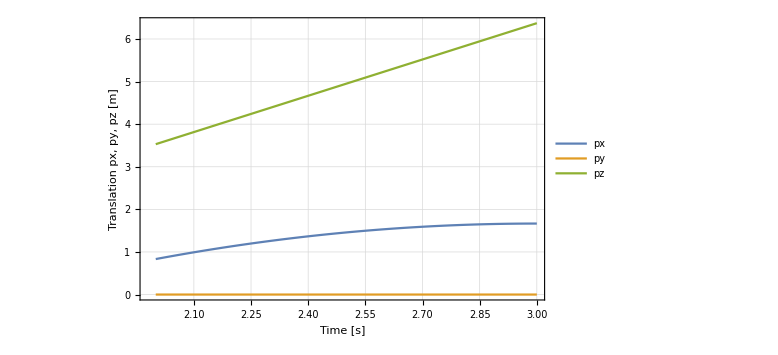
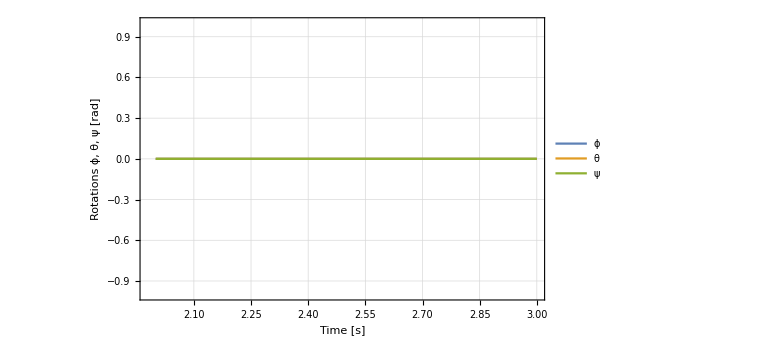
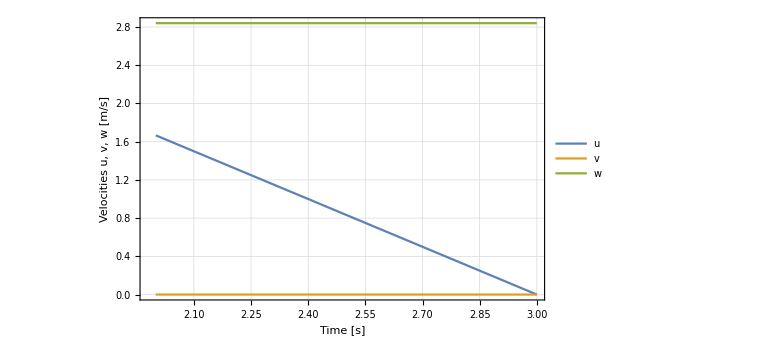
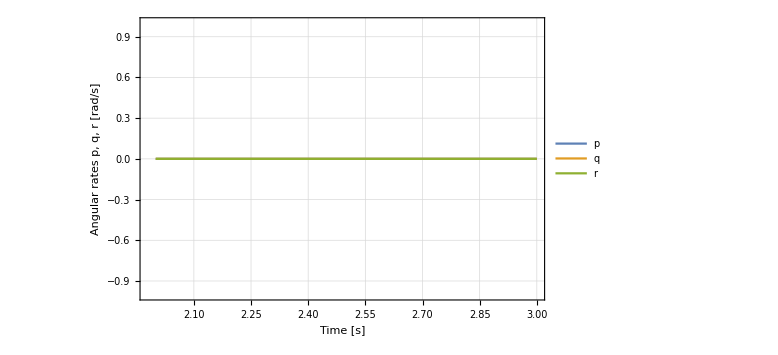
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
{time1,{sol,ci4,eqssystem}}=AbsoluteTiming[ivpPlant1[eqs,Flatten[{velocities,angrates,translation,rotation}],t,{{g,9.80665},{m,3}},{{fx,-5},{fy,0},{fz,3 9.80665 1},{tx,0},{ty,0},{tz,0}},{2,3},cis3,100]];
{{time1,graphposition},{time2,graphatitude}}={AbsoluteTiming[graphics2[sol,{"px [m]","py [m]","pz [m]"},1,{"Time [s]","Translation px, py, pz [m]"},{8,9,10}]],AbsoluteTiming[graphics2[sol,{"ϕ [rad]","θ [rad]","ψ [rad]"},1,{"Time [s]","Rotations ϕ, θ, ψ [rad]"},{11,12,13}]]};
graftranslationsvstime=graphics1[sol,{"px","py","pz"},1,{"Time [s]","Translation px, py, pz [m]"},{8,9,10}];
grafrotarionsvstime=graphics1[sol,{"ϕ","θ","ψ"},1,{"Time [s]","Rotations ϕ, θ, ψ [rad]"},{11,12,13}];
grafvelocityvstime=graphics1[sol,{"u","v","w"},1,{"Time [s]","Velocities u, v, w [m/s]"},{2,3,4}];
grafomegavstime=graphics1[sol,{"p","q","r"},1,{"Time [s]","Angular rates p, q, r [rad/s]"},{5,6,7}];
eqssystem//MatrixForm//TraditionalForm
ci4[[1]];
time1"seconds"
time2"seconds"
(*grafveloc
grafvelocang*)
graftranslationsvstime;
grafrotarionsvstime;
grafvelocityvstime;
grafomegavstime;
grfcexerc3=Grid[Partition[{graftranslationsvstime,grafrotarionsvstime,grafvelocityvstime,grafomegavstime},2]]
```

Solution - Time interval = 3s - 4s
CI4

```mathematica
cis4=.;
cis4=Flatten[{variablesconditioning2[variablesconditioning1[velocities,3],ci4[[1]][[1;;3]]],variablesconditioning2[variablesconditioning1[angrates,3],ci4[[1]][[4;;6]]],variablesconditioning2[variablesconditioning1[translation,3],ci4[[1]][[7;;9]]],variablesconditioning2[variablesconditioning1[rotation,3],ci4[[1]][[10;;12]]]}];
```

(u'(t)==(fx cos(θ(t)) cos(ψ(t)))/m+(fy cos(θ(t)) sin(ψ(t)))/m-(fz sin(θ(t)))/m+q(t) w(t)-r(t) v(t)
v'(t)==(fx (sin(θ(t)) cos(ψ(t)) sin(ϕ(t))-sin(ψ(t)) cos(ϕ(t))))/m+(fy (sin(θ(t)) sin(ψ(t)) sin(ϕ(t))+cos(ψ(t)) cos(ϕ(t))))/m+(fz cos(θ(t)) sin(ϕ(t)))/m-p(t) w(t)+r(t) u(t)
w'(t)==(fx (sin(θ(t)) cos(ψ(t)) cos(ϕ(t))+sin(ψ(t)) sin(ϕ(t))))/m+(fy (sin(θ(t)) sin(ψ(t)) cos(ϕ(t))-cos(ψ(t)) sin(ϕ(t))))/m+(fz cos(θ(t)) cos(ϕ(t)))/m-g+p(t) v(t)-q(t) u(t)
p'(t)==1.25 tx+0.
q'(t)==1.25 ty+0.
r'(t)==1.25 tz+0.
px'(t)==(u(t) (cos(θ(t)) cos(ψ(t)) cos^2(ϕ(t))+cos(θ(t)) cos(ψ(t)) sin^2(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(v(t) (cos^2(θ(t)) sin(ψ(t)) (-cos(ϕ(t)))-sin^2(θ(t)) sin(ψ(t)) cos(ϕ(t))+sin(θ(t)) cos(ψ(t)) sin(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(w(t) (sin^2(θ(t)) sin(ψ(t)) sin(ϕ(t))+cos^2(θ(t)) sin(ψ(t)) sin(ϕ(t))+sin(θ(t)) cos(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))
py'(t)==(u(t) (cos(θ(t)) sin(ψ(t)) cos^2(ϕ(t))+cos(θ(t)) sin(ψ(t)) sin^2(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(v(t) (sin(θ(t)) sin(ψ(t)) sin(ϕ(t))+cos^2(θ(t)) cos(ψ(t)) cos(ϕ(t))+sin^2(θ(t)) cos(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(w(t) (cos^2(θ(t)) (-cos(ψ(t))) sin(ϕ(t))-sin^2(θ(t)) cos(ψ(t)) sin(ϕ(t))+sin(θ(t)) sin(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))
pz'(t)==(u(t) (-sin(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))-sin(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))-sin(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))-sin(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(v(t) (cos(θ(t)) cos^2(ψ(t)) sin(ϕ(t))+cos(θ(t)) sin^2(ψ(t)) sin(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(w(t) (cos(θ(t)) cos^2(ψ(t)) cos(ϕ(t))+cos(θ(t)) sin^2(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))
ϕ'(t)==p(t)+q(t) tan(θ(t)) cos(ϕ(t))-r(t) tan(θ(t)) sin(ϕ(t))
θ'(t)==q(t) cos(ϕ(t))-r(t) sin(ϕ(t))
ψ'(t)==q(t) sin(ϕ(t) sec(θ(t)))+r(t) sec(θ(t)) cos(ϕ(t))
u(3)==2.77556×10^-17
v(3)==0.
w(3)==2.84068
p(3)==0.
q(3)==0.
r(3)==0.
px(3)==1.66667
py(3)==0.
pz(3)==6.37104
ϕ(3)==0.
θ(3)==0.
ψ(3)==0.)

0.240856 seconds

0.193266 seconds

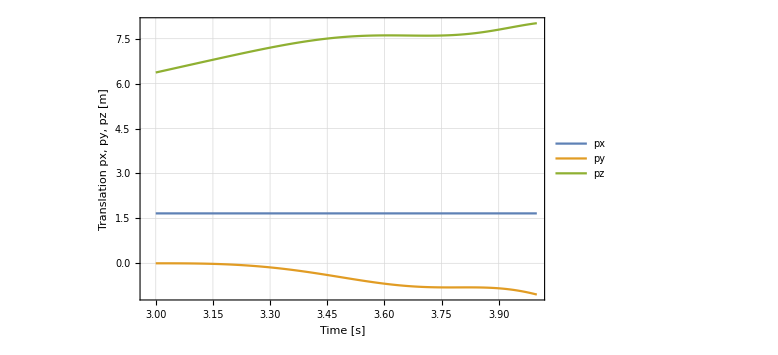
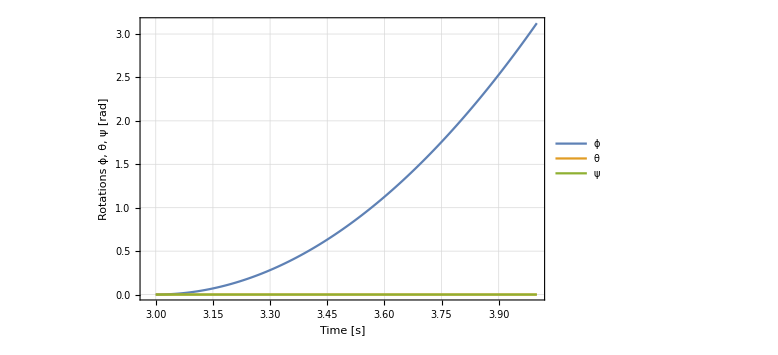
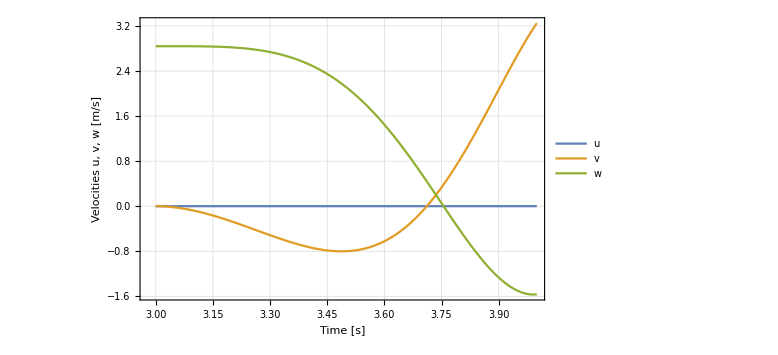
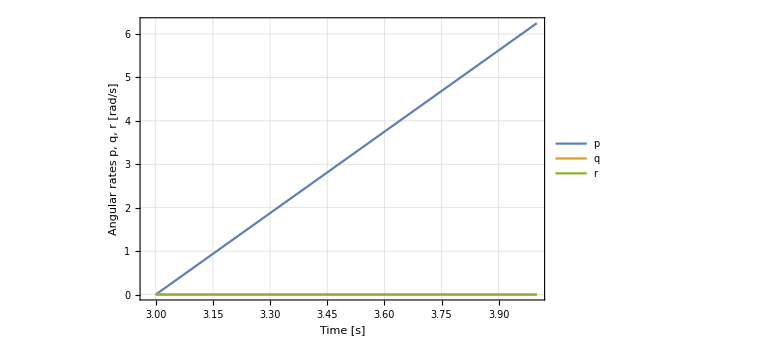
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
{time1,{sol,ci5,eqssystem}}=AbsoluteTiming[ivpPlant1[eqs,Flatten[{velocities,angrates,translation,rotation}],t,{{g,9.80665},{m,3}},{{fx,0},{fy,0},{fz,3 9.80665 1.0},{tx,5},{ty,0},{tz,0}},{3,4},cis4,100]];
{{time1,graphposition},{time2,graphatitude}}={AbsoluteTiming[graphics2[sol,{"px [m]","py [m]","pz [m]"},1,{"Time [s]","Translation px, py, pz [m]"},{8,9,10}]],AbsoluteTiming[graphics2[sol,{"ϕ [rad]","θ [rad]","ψ [rad]"},1,{"Time [s]","Rotations ϕ, θ, ψ [rad]"},{11,12,13}]]};
graftranslationsvstime=graphics1[sol,{"px","py","pz"},1,{"Time [s]","Translation px, py, pz [m]"},{8,9,10}];
grafrotarionsvstime=graphics1[sol,{"ϕ","θ","ψ"},1,{"Time [s]","Rotations ϕ, θ, ψ [rad]"},{11,12,13}];
grafvelocityvstime=graphics1[sol,{"u","v","w"},1,{"Time [s]","Velocities u, v, w [m/s]"},{2,3,4}];
grafomegavstime=graphics1[sol,{"p","q","r"},1,{"Time [s]","Angular rates p, q, r [rad/s]"},{5,6,7}];
eqssystem//MatrixForm//TraditionalForm
ci4[[1]];
time1"seconds"
time2"seconds"
(*grafveloc
grafvelocang*)
graftranslationsvstime;
grafrotarionsvstime;
grafvelocityvstime;
grafomegavstime;
grfcexerc4=Grid[Partition[{graftranslationsvstime,grafrotarionsvstime,grafvelocityvstime,grafomegavstime},2]]
```

Solution - Time interval = 4s - 5s
CI5

```mathematica
3 9.80665 1.15
```

33.8329

```mathematica
cis5=.;
cis5=Flatten[{variablesconditioning2[variablesconditioning1[velocities,4],ci5[[1]][[1;;3]]],variablesconditioning2[variablesconditioning1[angrates,4],ci5[[1]][[4;;6]]],variablesconditioning2[variablesconditioning1[translation,4],ci5[[1]][[7;;9]]],variablesconditioning2[variablesconditioning1[rotation,4],ci5[[1]][[10;;12]]]}];
```

(u'(t)==(fx cos(θ(t)) cos(ψ(t)))/m+(fy cos(θ(t)) sin(ψ(t)))/m-(fz sin(θ(t)))/m+q(t) w(t)-r(t) v(t)
v'(t)==(fx (sin(θ(t)) cos(ψ(t)) sin(ϕ(t))-sin(ψ(t)) cos(ϕ(t))))/m+(fy (sin(θ(t)) sin(ψ(t)) sin(ϕ(t))+cos(ψ(t)) cos(ϕ(t))))/m+(fz cos(θ(t)) sin(ϕ(t)))/m-p(t) w(t)+r(t) u(t)
w'(t)==(fx (sin(θ(t)) cos(ψ(t)) cos(ϕ(t))+sin(ψ(t)) sin(ϕ(t))))/m+(fy (sin(θ(t)) sin(ψ(t)) cos(ϕ(t))-cos(ψ(t)) sin(ϕ(t))))/m+(fz cos(θ(t)) cos(ϕ(t)))/m-g+p(t) v(t)-q(t) u(t)
p'(t)==1.25 tx+0.
q'(t)==1.25 ty+0.
r'(t)==1.25 tz+0.
px'(t)==(u(t) (cos(θ(t)) cos(ψ(t)) cos^2(ϕ(t))+cos(θ(t)) cos(ψ(t)) sin^2(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(v(t) (cos^2(θ(t)) sin(ψ(t)) (-cos(ϕ(t)))-sin^2(θ(t)) sin(ψ(t)) cos(ϕ(t))+sin(θ(t)) cos(ψ(t)) sin(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(w(t) (sin^2(θ(t)) sin(ψ(t)) sin(ϕ(t))+cos^2(θ(t)) sin(ψ(t)) sin(ϕ(t))+sin(θ(t)) cos(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))
py'(t)==(u(t) (cos(θ(t)) sin(ψ(t)) cos^2(ϕ(t))+cos(θ(t)) sin(ψ(t)) sin^2(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(v(t) (sin(θ(t)) sin(ψ(t)) sin(ϕ(t))+cos^2(θ(t)) cos(ψ(t)) cos(ϕ(t))+sin^2(θ(t)) cos(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(w(t) (cos^2(θ(t)) (-cos(ψ(t))) sin(ϕ(t))-sin^2(θ(t)) cos(ψ(t)) sin(ϕ(t))+sin(θ(t)) sin(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))
pz'(t)==(u(t) (-sin(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))-sin(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))-sin(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))-sin(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(v(t) (cos(θ(t)) cos^2(ψ(t)) sin(ϕ(t))+cos(θ(t)) sin^2(ψ(t)) sin(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))+(w(t) (cos(θ(t)) cos^2(ψ(t)) cos(ϕ(t))+cos(θ(t)) sin^2(ψ(t)) cos(ϕ(t))))/(sin^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+sin^2(θ(t)) cos^2(ψ(t)) sin^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+sin^2(θ(t)) sin^2(ψ(t)) cos^2(ϕ(t))+cos^2(θ(t)) sin^2(ψ(t)) sin^2(ϕ(t)))
ϕ'(t)==p(t)+q(t) tan(θ(t)) cos(ϕ(t))-r(t) tan(θ(t)) sin(ϕ(t))
θ'(t)==q(t) cos(ϕ(t))-r(t) sin(ϕ(t))
ψ'(t)==q(t) sin(ϕ(t) sec(θ(t)))+r(t) sec(θ(t)) cos(ϕ(t))
u(4)==2.77556×10^-17
v(4)==3.24953
w(4)==-1.56599
p(4)==6.25
q(4)==0.
r(4)==0.
px(4)==1.66667
py(4)==-1.04316
pz(4)==8.01832
ϕ(4)==3.125
θ(4)==0.
ψ(4)==0.)

0.244354 seconds

0.198859 seconds

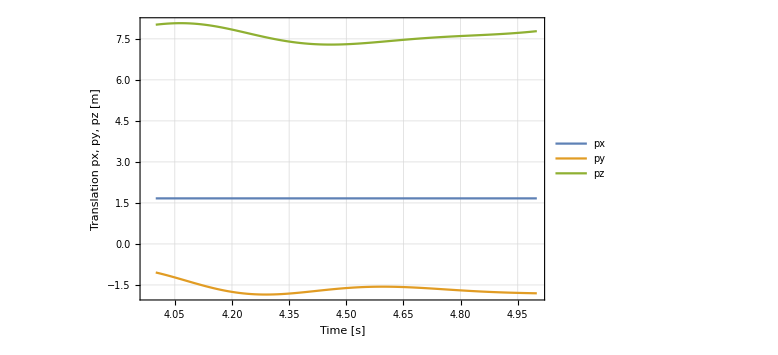
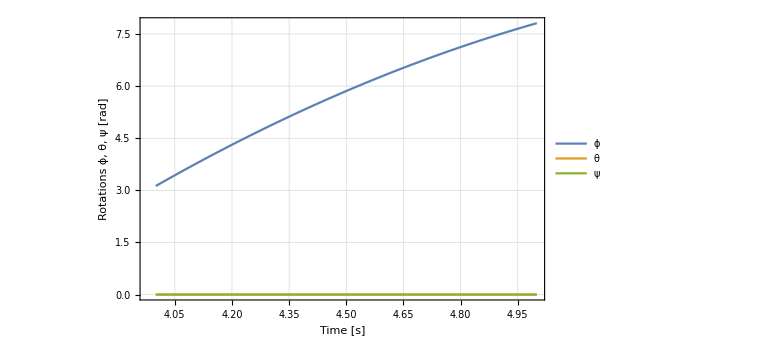
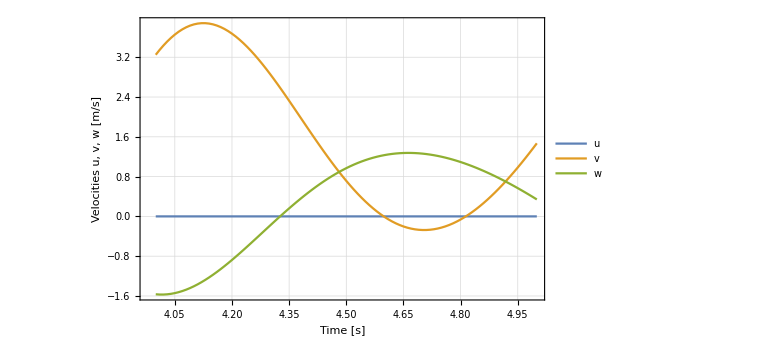
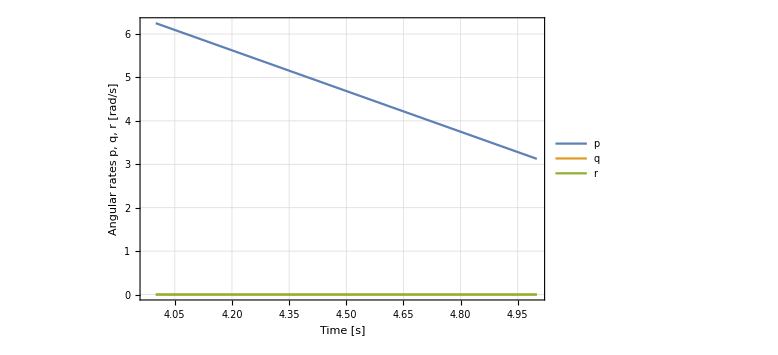
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
{time1,{sol,ci6,eqssystem}}=AbsoluteTiming[ivpPlant1[eqs,Flatten[{velocities,angrates,translation,rotation}],t,{{g,9.80665},{m,3}},{{fx,0},{fy,0},{fz,3 9.80665 1.15},{tx,-2.5},{ty,0},{tz,0}},{4,5},cis5,100]];
{{time1,graphposition},{time2,graphatitude}}={AbsoluteTiming[graphics2[sol,{"px [m]","py [m]","pz [m]"},1,{"Time [s]","Translation px, py, pz [m]"},{8,9,10}]],AbsoluteTiming[graphics2[sol,{"ϕ [rad]","θ [rad]","ψ [rad]"},1,{"Time [s]","Rotations ϕ, θ, ψ [rad]"},{11,12,13}]]};
graftranslationsvstime=graphics1[sol,{"px","py","pz"},1,{"Time [s]","Translation px, py, pz [m]"},{8,9,10}];
grafrotarionsvstime=graphics1[sol,{"ϕ","θ","ψ"},1,{"Time [s]","Rotations ϕ, θ, ψ [rad]"},{11,12,13}];
grafvelocityvstime=graphics1[sol,{"u","v","w"},1,{"Time [s]","Velocities u, v, w [m/s]"},{2,3,4}];
grafomegavstime=graphics1[sol,{"p","q","r"},1,{"Time [s]","Angular rates p, q, r [rad/s]"},{5,6,7}];
eqssystem//MatrixForm//TraditionalForm
ci6[[1]];
time1"seconds"
time2"seconds"
(*grafveloc
grafvelocang*)
graftranslationsvstime;
grafrotarionsvstime;
grafvelocityvstime;
grafomegavstime;
grfcexerc5=Grid[Partition[{graftranslationsvstime,grafrotarionsvstime,grafvelocityvstime,grafomegavstime},2]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"grafforcemomentconst_1.png"}],grfcexerc1]
Export[FileNameJoin[{NotebookDirectory[],"grafforcemomentconst_2.png"}],grfcexerc2]
Export[FileNameJoin[{NotebookDirectory[],"grafforcemomentconst_3.png"}],grfcexerc3]
Export[FileNameJoin[{NotebookDirectory[],"grafforcemomentconst_4.png"}],grfcexerc4]
Export[FileNameJoin[{NotebookDirectory[],"grafforcemomentconst_5.png"}],grfcexerc5]
```

D:\fabio\OneDrive\cursos\puc\00_DISSERTAÇÃO\04_Desenvolvimentos\C_Modelagens\Dinâmica\WorkFiles\grafforcemomentconst_1.png

D:\fabio\OneDrive\cursos\puc\00_DISSERTAÇÃO\04_Desenvolvimentos\C_Modelagens\Dinâmica\WorkFiles\grafforcemomentconst_2.png

D:\fabio\OneDrive\cursos\puc\00_DISSERTAÇÃO\04_Desenvolvimentos\C_Modelagens\Dinâmica\WorkFiles\grafforcemomentconst_3.png

D:\fabio\OneDrive\cursos\puc\00_DISSERTAÇÃO\04_Desenvolvimentos\C_Modelagens\Dinâmica\WorkFiles\grafforcemomentconst_4.png

D:\fabio\OneDrive\cursos\puc\00_DISSERTAÇÃO\04_Desenvolvimentos\C_Modelagens\Dinâmica\WorkFiles\grafforcemomentconst_5.png

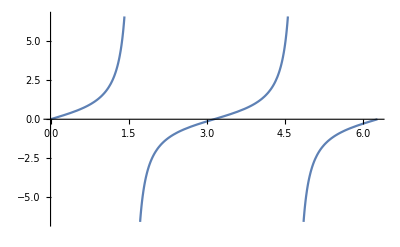

```mathematica
Plot[Tan[x],{x,0,2 π}]
```

## Space State Analisys